# Schwinger Model

## Background / Initialization

Let us first understand the (1+1)-d Schwinger model. The Hamiltonian reads
 
                                     H = ∑_(n=1)^(N-1) ((χ^†)_n χ_(n+1)-(χ^†)_(n+1)χ_n)+m∑_(n=1)^N (-1)^n∑_(n=1)^(N-1) (χ^†)_n χ_n+(a g^2)/2∑_(n=1)^(N-1) (L_(dyn,n)+L_(ext,n)(t))^2,
                                             L_(dyn,n)=∑_(i=1)^n q_i,      L_(ext,n)(t) = -θ((t-t_0)/a-|n-N/□|),     q_i=n_i+((-1)^i-1)/2, n_i=(χ^†)_i χ_i          (1)

where n=1...N labels the lattice sites,  (χ^†)_n is the fermionic creation operator, a is the lattice spacing, and m and g are the fermion mass and electric charge, respectively. We note that the fermions described above are staggered fermions, although for our purposes here in Mathematica that won’t be directly relevant.

### Creation/annihilation operators

What is the form of the fermionic creation/annihilation operators generated by the fermionic algebra and Fock space? Recall fermions obey the anti-commutation relations
                                                       {χ,χ^†} = 1,    {χ,χ} = {χ^†,χ^†} = 0 ⧦ χχ  =  χ^†χ^† = 0   
This immediately implies that 
                                                                      				n(1-n) = χ^†χ χ χ^† = 0   ⧦   n = 0, 1 
are the only allowed occupation numbers for fermions. This is the “Pauli principle”. Hence
								χ|0> = 0,       χ^†|0> = |1>,        χ|1> = |0>,       χ^†|1> = 0,
or in matrix notation
								χ = (0 | 1
0 | 0),     χ^† = (0 | 0
1 | 0) for    |0> = (1
0),     |1> = (0
1).

Recall that when dealing with tensor products, the operator χ_n=1⊗...⊗χ⊗1⊗...⊗1 where χ is in the n-th position. Hence, the fermion creation/annihilation operators are constructed through

The fermionic commutation relations are given by {χ_i,χ_j}={(χ^†)_i,(χ^†)_j}=0, {χ_i,(χ^†)_j}=δ_ij, or

(χ^†)_i|n_1,...,n_i,...,n_N>={(-1)^(∑_(j<i) n_j)|n_1,...,n_i+1,...,n_N>,       n_i=0
0 ,                                                                                 n_i=1  ;      χ_i|n_1,...,n_i,...,n_N>={(-1)^(∑_(j<i) n_j)|n_1,...,n_i-1,...,n_N>,      n_i=0
0,                                                                                 n_i=1.
We need to ensure that this algebra is obeyed.

```mathematica
Clear[χ,χd,tempχd,adj,adjzeros,toexpr,table,tempans]
χd[N0_,n0_]:=Module[{N=N0,n=n0},
tempχd=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,0},{1,0}}, IdentityMatrix[2^(N-n)]]],2]];
adj=SparseArray[tempχd]["AdjacencyLists"];
adjzeros=adj/.{}->0;
toexpr=ToExpression[Table[Characters@IntegerString[adjzeros[[i]]-1,2,N][[1]],{i,1,2^N}]]//Quiet;
table=Table[Sum[toexpr[[i]][[j]],{j,1,n}],{i,1,2^N}]//Quiet;
tempans=Table[(*ⅈ**)(-1)^table[[i]],{i,1,2^N}];
Table[tempχd[[i,j]]*tempans[[i]],{i,1,2^N},{j,1,2^N}]]
χ[N0_,n0_]:=χ[N0,n0]=ConjugateTranspose[χd[N0,n0]]
```

```mathematica
χ[2,1].χd[2,1]+((-1)^1-1)/2*IdentityMatrix[4]//MatrixForm (*Subscript[q, 1]*)
χ[2,2].χd[2,2]+((-1)^2-1)/2*IdentityMatrix[4]//MatrixForm(*Subscript[q, 2]*)
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

```mathematica
χ[2,1].χd[2,1]//MatrixForm
TensorProduct[PauliMatrix[3],IdentityMatrix[2]]//ArrayFlatten//MatrixForm
χ[2,2].χd[2,2]//MatrixForm
TensorProduct[IdentityMatrix[2],PauliMatrix[3]]//ArrayFlatten//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
(-1*TensorProduct[PauliMatrix[3],IdentityMatrix[2]]+TensorProduct[IdentityMatrix[2],PauliMatrix[3]])*1/2//ArrayFlatten//MatrixForm
```

(0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

Commutator checks

```mathematica
Commutator[a_,b_]:=a.b-b.a
AntiCommutator[a_,b_]:=a.b+b.a
```

```mathematica
AntiCommutator[χ[2,1],χ[2,1]]//MatrixForm
AntiCommutator[χ[2,1],χd[2,1]]//MatrixForm
AntiCommutator[χd[2,1],χd[2,2]]//MatrixForm
AntiCommutator[χ[3,2],χ[3,2]]//MatrixForm
AntiCommutator[χ[3,2],χd[3,2]]//MatrixForm
AntiCommutator[χd[3,2],χd[3,2]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(PauliMatrix[1]+ⅈ*PauliMatrix[2])/2
(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2
```

{{0,1},{0,0}}

{{0,0},{1,0}}

```mathematica
TensorProduct[{{},{}},{{},{}}]
```

Let’s check that the Jordan-Wigner transformation is given by
														(χ^†)_j=(∏_(k=1)^(j-1) Z_k)(σ^-)_j,     χ_j=(∏_(k=1)^(j-1) Z_k)(σ^+)_j.

```mathematica
Clear[SigmaX,SigmaY,SigmaZ,SigmaMinusOpN,SigmaPlusOpN]
SigmaX[N_,n_]:=SigmaX[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[1], IdentityMatrix[2^(N-n)]]],2]];
SigmaY[N_,n_]:=SigmaY[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[2], IdentityMatrix[2^(N-n)]]],2]];
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
SigmaMinusOpN[N_,n_]:=SigmaMinusOpN[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2, IdentityMatrix[2^(N-n)]]],2]];
SigmaPlusOpN[N_,n_]:=SigmaPlusOpN[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],(PauliMatrix[1]+ⅈ*PauliMatrix[2])/2, IdentityMatrix[2^(N-n)]]],2]];
```

```mathematica
SigmaPlusOpN[2,1]+SigmaPlusOpN[2,2].SigmaZ[2,1]*ⅈ
SigmaMinusOpN[2,1]+ⅈ*SigmaZ[2,1].SigmaMinusOpN[2,2]
-SigmaPlusOpN[2,1].SigmaMinusOpN[2,1]+(SigmaPlusOpN[2,2].SigmaZ[2,1]*ⅈ).(SigmaMinusOpN[2,2].SigmaZ[2,1]*(-ⅈ))//MatrixForm
```

{{0,ⅈ,1,0},{0,0,0,1},{0,0,0,-ⅈ},{0,0,0,0}}

{{0,0,0,0},{ⅈ,0,0,0},{1,0,0,0},{0,1,-ⅈ,0}}

(0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

```mathematica
SigmaZ[3,1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
SigmaPlusOpN[2,1]+ⅈ*SigmaZ[2,1].SigmaPlusOpN[2,2]//MatrixForm
```

(0 | ⅈ | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0)

```mathematica
χ[2,1]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ArrayFlatten[χd[4,1]]//MatrixForm;
ArrayFlatten[ArrayFlatten[TensorProduct[(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2,IdentityMatrix[2^3]]]]//MatrixForm;
%==%%
```

True

```mathematica
ArrayFlatten[χd[4,2]]//MatrixForm;
ArrayFlatten[ArrayFlatten[TensorProduct[PauliMatrix[3],(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2,IdentityMatrix[2^2]]]]//MatrixForm;
%==%%
```

True

```mathematica
ArrayFlatten[χd[4,3]]//MatrixForm;
ArrayFlatten[ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[PauliMatrix[3],PauliMatrix[3]]],(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2,{{1,0},{0,1}}]]]//MatrixForm;
%==%%
```

True

```mathematica
ArrayFlatten[χd[4,4]]//MatrixForm;
ArrayFlatten[ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[PauliMatrix[3],PauliMatrix[3],PauliMatrix[3]]],(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2]]]//MatrixForm;
%==%%
```

True

Check mass term

```mathematica
Clear[SigmaZ]
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
```

```mathematica
-χ[2,1].χd[2,1]+χ[2,2].χd[2,2]//MatrixForm
-1/2 SigmaZ[2,1]+1/2 SigmaZ[2,2]//MatrixForm
```

(0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

### Hamiltonian

Construct the Hamiltonian in eq. 1.

```mathematica
Clear[χ,χd,H1,H2,Ldyn,Lext,Helec,HamSchw,temp,temp1,temp2,temp3]

χd[N0_,n0_]:=Module[{N=N0,n=n0},
tempχd=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,0},{1,0}}, IdentityMatrix[2^(N-n)]]],2]];
adj=SparseArray[tempχd]["AdjacencyLists"];
adjzeros=adj/.{}->0;
toexpr=ToExpression[Table[Characters@IntegerString[adjzeros[[i]]-1,2,N][[1]],{i,1,2^N}]]//Quiet;
table=Table[Sum[toexpr[[i]][[j]],{j,1,n}],{i,1,2^N}]//Quiet;
tempans=Table[(-1)^table[[i]],{i,1,2^N}];
Table[tempχd[[i,j]]*tempans[[i]],{i,1,2^N},{j,1,2^N}]]
χ[N0_,n0_]:=χ[N0,n0]=ConjugateTranspose[χd[N0,n0]]

H1[N0_]:=Module[{N=N0},
temp=Sum[ArrayFlatten[χd[N,n].χ[N,n+1]-χd[N,n+1].χ[N,n],2],{n,1,N-1}](*+χd[num,num].χ[num,1]*);
temp]

H2[N0_]:=Module[{N=N0},
temp1=Sum[ArrayFlatten[(-1)^n*χd[N,n].χ[N,n],2],{n,1,N}](*+χd[num,num].χ[num,1]*);
temp1]

Ldyn[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_,i_]:=q[N,n,i] =Sum[ArrayFlatten[χd[N,i].χ[N,i]]+((-1)^i-1)/2,{i,1,n}];
temp2 = Sum[q[N,n,i],{n,1,N-1}];
temp2]

Lext[N0_,n0_,t0_,ti0_,a0_]:=Module[{N=N0,n=n0,t=t0,ti=ti0,a=a0},
temp3 = -HeavisideTheta[(t-ti)/a-Abs[n-N/2]]*IdentityMatrix[2^N];
temp3]

Helec[N0_,t0_,ti0_,a0_]:=Module[{N=N0,t=t0,ti=ti0,a=a0},
temp4=Sum[(Ldyn[N,n]+Lext[N,n,t,ti,a])^2,{n,1,N-1}];
temp4]

HamSchw[N_,t_,ti_,m_,a_,g_]:=HamSchw[N,t,ti,m,a,g]=-ⅈ/(2a)H1[N]+m H2[N]+(a g^2)/2 Helec[N,t,ti,a]
```

```mathematica
ArrayFlatten[χd[2,1].χ[2,1]]//MatrixForm
ArrayFlatten[χd[2,2].χ[2,2]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
ArrayFlatten[χd[2,2]]//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1 | 0)

```mathematica
ArrayFlatten[ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[PauliMatrix[3],PauliMatrix[3],PauliMatrix[3]]],(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
Clear[SigmaX,SigmaY,SigmaZ,SigmaIZ]
SigmaX[N_,n_]:=SigmaX[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[1], IdentityMatrix[2^(N-n)]]],2]];
SigmaY[N_,n_]:=SigmaY[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[2], IdentityMatrix[2^(N-n)]]],2]];
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
SigmaIZ[N_,n_]:=SigmaIZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],IdentityMatrix[2]-PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
```

```mathematica
SigmaIZ[2,2]/2//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
SigmaZ[2,1]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
ArrayFlatten[TensorProduct[PauliMatrix[3],IdentityMatrix[2]]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Clear[Ldyn, q]
Ldyn[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_,i_]:=q[N,n,i] =Sum[(*ArrayFlatten[χd[N,i].χ[N,i]]*)SigmaIZ[N,n]+((-1)^i-1)/2,{i,1,n}];
temp2 = Sum[q[N,n,i],{n,1,N-1}];
temp2]
```

```mathematica
SigmaIZ[2,1]/2+((-1)^1-1)/2*IdentityMatrix[4]+SigmaIZ[2,2]/2+((-1)^2-1)/2*IdentityMatrix[4]//FullSimplify//MatrixForm
χd[2,1].χ[2,1]+((-1)^1-1)/2*IdentityMatrix[4]+χd[2,2].χ[2,2]+((-1)^2-1)/2*IdentityMatrix[4]//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

(-1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
a1*SigmaZ[2,1].SigmaX[2,1]+a2*SigmaZ[2,1].SigmaY[2,1]+a3*SigmaZ[2,1].SigmaZ[2,1]+a4*SigmaX[2,1].SigmaY[2,1]+a5*SigmaX[2,1].SigmaZ[2,1]+a6*SigmaY[2,1].SigmaZ[2,1]//MatrixForm
Solve[%==({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}),{a1,a2,a3,a4,a5,a6}]
```

(-ⅈ a1+ⅈ a2+a3+ⅈ a4+a5+a6 | 0 | 0 | 0
0 | -ⅈ a1+ⅈ a2+a3+ⅈ a4+a5+a6 | 0 | 0
0 | 0 | ⅈ a1-ⅈ a2+a3-ⅈ a4+a5+a6 | 0
0 | 0 | 0 | ⅈ a1-ⅈ a2+a3-ⅈ a4+a5+a6)

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a4→ⅈ/2+a1-a2,a6→1/2-a3-a5}}

```mathematica
a1*SigmaZ[2,2].SigmaX[2,2]+a2*SigmaZ[2,2].SigmaY[2,2]+a3*SigmaZ[2,2].SigmaZ[2,2]//MatrixForm
Solve[%==({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}}),{a1,a2,a3}]
```

(-ⅈ a1+ⅈ a2+a3 | 0 | 0 | 0
0 | ⅈ a1-ⅈ a2+a3 | 0 | 0
0 | 0 | -ⅈ a1+ⅈ a2+a3 | 0
0 | 0 | 0 | ⅈ a1-ⅈ a2+a3)

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a2→ⅈ/2+a1,a3→1/2}}

```mathematica
0*SigmaZ[2,1].SigmaX[2,1]+a2*SigmaZ[2,2].SigmaY[2,2]+a3*SigmaZ[2,2].SigmaZ[2,2]/.{a1->0,a2->ⅈ/2,a3->1/2}//MatrixForm
```

(1/2+ⅈ/2 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 0 | 0
0 | 0 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1/2+ⅈ/2)

```mathematica
MM=2;mm=2;
ArrayFlatten[χd[MM,mm].χ[MM,mm]]//MatrixForm
ⅈ/2*SigmaZ[MM,1].SigmaY[MM,1]+1/2*SigmaZ[MM,1].SigmaZ[MM,1]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

(1/2+ⅈ/2 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 0 | 0
0 | 0 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1/2+ⅈ/2)

```mathematica
HamSchw[3,0,0,0,1,0]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
HamSchw[2,10,0,1,1,1]//MatrixForm
```

(2 | 1/2 | 1/2 | 1/2
1/2 | 3 | 1/2+ⅈ/2 | 1/2
1/2 | 1/2-ⅈ/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | 1/2)

```mathematica
χd[3,2]//MatrixForm
χd[3,3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
IdentityMatrix[1/2]
```

IdentityMatrix::dims: Dimension specification 1/2 should be a positive machine integer or a pair of positive machine integers.

IdentityMatrix[1/2]

```mathematica
Table[ArrayFlatten[χd[3,n].χ[3,n+1]-χd[3,n+1].χ[3,n],2],{n,1,2}](*+χd[num,num].χ[num,1]*);
```

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[-ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[«2»]],2]].{{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0}}.ArrayFlatten[ArrayFlatten[ArrayFlatten[{«4»}⊗ArrayFlatten[«1»]],2]],2] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

Let’s be cheeky and simply solve for the Pauli decomposition and see if it matches our expectation from Jordan-Wigner.

```mathematica
p1=ArrayFlatten[TensorProduct[PauliMatrix[1],PauliMatrix[1]]];
p2=ArrayFlatten[TensorProduct[PauliMatrix[1],PauliMatrix[2]]];
p3=ArrayFlatten[TensorProduct[PauliMatrix[1],PauliMatrix[3]]];
p4=ArrayFlatten[TensorProduct[PauliMatrix[2],PauliMatrix[1]]];
p5=ArrayFlatten[TensorProduct[PauliMatrix[2],PauliMatrix[2]]];
p6=ArrayFlatten[TensorProduct[PauliMatrix[2],PauliMatrix[3]]];
p7=ArrayFlatten[TensorProduct[PauliMatrix[3],PauliMatrix[1]]];
p8=ArrayFlatten[TensorProduct[PauliMatrix[3],PauliMatrix[2]]];
p9=ArrayFlatten[TensorProduct[PauliMatrix[3],PauliMatrix[3]]];
p10=ArrayFlatten[TensorProduct[IdentityMatrix[2],PauliMatrix[1]]];
p11=ArrayFlatten[TensorProduct[IdentityMatrix[2],PauliMatrix[2]]];
p12=ArrayFlatten[TensorProduct[IdentityMatrix[2],PauliMatrix[3]]];
p13=ArrayFlatten[TensorProduct[PauliMatrix[1],IdentityMatrix[2]]];
p14=ArrayFlatten[TensorProduct[PauliMatrix[2],IdentityMatrix[2]]];
p15=ArrayFlatten[TensorProduct[PauliMatrix[3],IdentityMatrix[2]]];
p16=ArrayFlatten[TensorProduct[IdentityMatrix[2],IdentityMatrix[2]]];
```

```mathematica
p1*c1+p2*c2+p3*c3+p4*c4+p5*c5+p6*c6+p7*c7+p8*c8+p9*c9+p10*c10+p11*c11+p12*c12+p13*c13+p14*c14+p15*c15+p16*c16
%//MatrixForm;
sol=Solve[%%==HamSchw[2,10,0,1,1,1],{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16}]
```

{{c12+c15+c16+c9,c10-ⅈ c11+c7-ⅈ c8,c13-ⅈ c14+c3-ⅈ c6,c1-ⅈ c2-ⅈ c4-c5},{c10+ⅈ c11+c7+ⅈ c8,-c12+c15+c16-c9,c1+ⅈ c2-ⅈ c4+c5,c13-ⅈ c14-c3+ⅈ c6},{c13+ⅈ c14+c3+ⅈ c6,c1-ⅈ c2+ⅈ c4+c5,c12-c15+c16-c9,c10-ⅈ c11-c7+ⅈ c8},{c1+ⅈ c2+ⅈ c4-c5,c13+ⅈ c14-c3-ⅈ c6,c10+ⅈ c11-c7-ⅈ c8,-c12-c15+c16+c9}}

{{c1→1/2,c2→1/4,c3→0,c4→-1/4,c5→0,c6→0,c7→0,c8→0,c9→0,c10→1/2,c11→0,c12→-1/2,c13→1/2,c14→0,c15→5/4,c16→5/4}}

```mathematica
coeffs={c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16};
paulis={XX,XY,XZ,YX,YY,YZ,ZX,ZY,ZZ,IX,IY,IZ,XI,YI,ZI,II};
```

```mathematica
Inner[Times,coeffs,paulis]/.sol
```

{(5 II)/4+IX/2-IZ/2+XI/2+XX/2+XY/4-YX/4+(5 ZI)/4}

```mathematica
p1*c1+p2*c2+p3*c3+p4*c4+p5*c5+p6*c6+p7*c7+p8*c8+p9*c9+p10*c10+p11*c11+p12*c12+p13*c13+p14*c14+p15*c15+p16*c16
%//MatrixForm;
sol=Solve[%%==χd[2,2].χ[2,2],{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16}]
```

{{c12+c15+c16+c9,c10-ⅈ c11+c7-ⅈ c8,c13-ⅈ c14+c3-ⅈ c6,c1-ⅈ c2-ⅈ c4-c5},{c10+ⅈ c11+c7+ⅈ c8,-c12+c15+c16-c9,c1+ⅈ c2-ⅈ c4+c5,c13-ⅈ c14-c3+ⅈ c6},{c13+ⅈ c14+c3+ⅈ c6,c1-ⅈ c2+ⅈ c4+c5,c12-c15+c16-c9,c10-ⅈ c11-c7+ⅈ c8},{c1+ⅈ c2+ⅈ c4-c5,c13+ⅈ c14-c3-ⅈ c6,c10+ⅈ c11-c7-ⅈ c8,-c12-c15+c16+c9}}

{{c1→0,c2→0,c3→0,c4→0,c5→0,c6→0,c7→0,c8→0,c9→0,c10→0,c11→0,c12→-1/2,c13→0,c14→0,c15→0,c16→1/2}}

```mathematica
Inner[Times,coeffs,paulis]/.sol
```

{II/2-IZ/2}

#### Jordan-Wigner Transformation

The Jordan-Wigner transformation maps spin operators (which let us put it on the quantum hardware easily) and fermionic creation/annihilation operators via the transformation
											(χ^†)_j=∏_(l<j) (ⅈ (σ^z)_l)(σ^-)_j,     χ_j=∏_(l<j) (-ⅈ (σ^z)_l)(σ^+)_j.

```mathematica
TensorZ[N0_]:=Module[{N=N0},
q[N_,n_,i_]:=q[N,n,i] =Sum[ArrayFlatten[χd[N,i].χ[N,i]]+((-1)^i-1)/2,{i,1,n}];
temp2 = Product[T];
temp2]
```

```mathematica
temp10=PauliMatrix[3];
Do[TensorProduct[PauliMatrix[3],temp10],3]
```

```mathematica
H1[2]//MatrixForm
p1*c1+p2*c2+p3*c3+p4*c4+p5*c5+p6*c6+p7*c7+p8*c8+p9*c9+p10*c10+p11*c11+p12*c12+p13*c13+p14*c14+p15*c15+p16*c16;
%//MatrixForm;
sol=Solve[%%==H1[2],{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16}];
Inner[Times,coeffs,paulis]/.sol
```

(0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0)

Inner::normal: Nonatomic expression expected at position 2 in Inner[Times,coeffs,paulis].

Inner[Times,coeffs,paulis]

```mathematica
H2[2]//MatrixForm
p1*c1+p2*c2+p3*c3+p4*c4+p5*c5+p6*c6+p7*c7+p8*c8+p9*c9+p10*c10+p11*c11+p12*c12+p13*c13+p14*c14+p15*c15+p16*c16;
%//MatrixForm;
sol=Solve[%%==H2[2],{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16}];
Inner[Times,coeffs,paulis]/.sol
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 0)

{-IZ/2+ZI/2}

```mathematica
Clear[SigmaPlus,SigmaMinus,SigmaPlusOp,SigmaMinusOp,H1bos,H2bos,Ldynbos,Lext,Helec,HamSchwBos,temp1,temp2,temp3,temp4]
SigmaPlus=(PauliMatrix[1]+ⅈ*PauliMatrix[2])/2;
SigmaMinus=(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2;
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
SigmaPlusOp[N_,n_]:=SigmaPlusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaPlus, IdentityMatrix[2^(N-n)]]],2]]
SigmaMinusOp[N_,n_]:=SigmaMinusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaMinus, IdentityMatrix[2^(N-n)]]],2]]

H1bos[N0_]:=Module[{N=N0},
temp=Sum[ArrayFlatten[SigmaPlusOp[N,n].SigmaMinusOp[N,n+1]-SigmaPlusOp[N,n+1].SigmaMinusOp[N,n],2],{n,1,N-1}](*+χd[num,num].χ[num,1]*);
temp]

(*H2bos[N0_]:=Module[{N=N0},
temp1=Sum[ArrayFlatten[-(-1)^n*SigmaPlusOp[N,n].SigmaMinusOp[N,n],2],{n,1,N}](*+χd[num,num].χ[num,1]*);
temp1]*)

H2bos[N0_]:=Module[{N=N0},
temp1=IdentityMatrix[2^N]+Sum[ArrayFlatten[(-1)^n SigmaZ[N,n],2],{n,1,N}];
temp1]

Ldynbos[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_,i_]:=q[N,n,i] =Sum[(*ArrayFlatten[SigmaPlusOp[N,i].SigmaMinusOp[N,i]]+*)((-1)^i-1)/2*IdentityMatrix[2^N],{i,1,n}];
temp2 = Sum[q[N,n,i],{n,1,N-1}];
temp2]

Lext[N0_,n0_,t0_,ti0_,a0_]:=Module[{N=N0,n=n0,t=t0,ti=ti0,a=a0},
temp3 = -HeavisideTheta[(t-ti)/a-Abs[n-N/2]]*IdentityMatrix[2^N];
temp3]

Helec[N0_,t0_,ti0_,a0_]:=Module[{N=N0,t=t0,ti=ti0,a=a0},
temp4=Sum[(Ldynbos[N,n]+Lext[N,n,t,ti,a])(*.(Ldynbos[N,n]+Lext[N,n,t,ti,a])*),{n,1,N-1}];
temp4]

HamSchwBos[N_,t_,ti_,m_,a_,g_]:=HamSchwBos[N,t,ti,m,a,g]=ⅈ/(2a)H1bos[N]-m/2 H2bos[N]+(a g^2)/2 Helec[N,t,ti,a]
```

```mathematica
LdynbosM[3,1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

```mathematica
Helec[3,0,0,1]//MatrixForm
```

(-4 | -4 | -4 | -4 | -4 | -4 | -4 | -4
-4 | -4 | -4 | -4 | -4 | -4 | -4 | -4
-4 | -4 | -2 | -4 | -4 | -4 | -4 | -4
-4 | -4 | -4 | -2 | -4 | -4 | -4 | -4
-4 | -4 | -4 | -4 | 0 | -4 | -4 | -4
-4 | -4 | -4 | -4 | -4 | 0 | -4 | -4
-4 | -4 | -4 | -4 | -4 | -4 | 2 | -4
-4 | -4 | -4 | -4 | -4 | -4 | -4 | 2)

```mathematica
HamSchw[3,10,0.1,1.1,1.4,1.6];
HamSchwBos[3,10,0.1,1.1,1.4,1.6];
%==%%
```

True

```mathematica
HamSchw[3,0,0,1.1,1.4,1.6];
HamSchwBos[3,0,0.1,1.1,1.4,1.6];
```

Another form

```mathematica
Clear[q,SigmaPlus,SigmaMinus,SigmaPlusOp,SigmaMinusOp,H1bosM,H2bosM,LdynbosM,LextM,HelecM,HamSchwBosM,temp1,temp2,temp3,temp4]
SigmaPlus=(PauliMatrix[1]+ⅈ*PauliMatrix[2])/2;
SigmaMinus=(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2;
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
SigmaPlusOp[N_,n_]:=SigmaPlusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaPlus, IdentityMatrix[2^(N-n)]]],2]]
SigmaMinusOp[N_,n_]:=SigmaMinusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaMinus, IdentityMatrix[2^(N-n)]]],2]]

H1bosM[N0_]:=Module[{N=N0},
temp=Sum[ArrayFlatten[SigmaPlusOp[N,n].SigmaMinusOp[N,n+1]-SigmaPlusOp[N,n+1].SigmaMinusOp[N,n],2],{n,1,N-1}](*+χd[num,num].χ[num,1]*);
temp]

(*H2bos[N0_]:=Module[{N=N0},
temp1=Sum[ArrayFlatten[-(-1)^n*SigmaPlusOp[N,n].SigmaMinusOp[N,n],2],{n,1,N}](*+χd[num,num].χ[num,1]*);
temp1]*)

H2bosM[N0_]:=Module[{N=N0},
temp1=IdentityMatrix[2^N]+Sum[ArrayFlatten[(-1)^n SigmaZ[N,n],2],{n,1,N}];
temp1]

LdynbosM[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_]:=q[N,n] =Sum[ArrayFlatten[SigmaPlusOp[N,i].SigmaMinusOp[N,i]]+((-1)^i-1)/2*IdentityMatrix[2^N],{i,1,n}];
temp2 = Sum[q[N,n],{n,1,N-1}];
temp2]

LextM[N0_,n0_,t0_,ti0_,a0_]:=Module[{N=N0,n=n0,t=t0,ti=ti0,a=a0},
temp3 = -HeavisideTheta[(t-ti)/a-Abs[n-N/2]]*IdentityMatrix[2^N];
temp3]

HelecM[N0_,t0_,ti0_,a0_]:=Module[{N=N0,t=t0,ti=ti0,a=a0},
temp4=Sum[(LdynbosM[N,n]+LextM[N,n,t,ti,a]).(LdynbosM[N,n]+LextM[N,n,t,ti,a]),{n,1,N-1}];
temp4]

HamSchwBosM[N_,t_,ti_,m_,a_,g_]:=HamSchwBosM[N,t,ti,m,a,g]=ⅈ/(2a)H1bosM[N]-m/2 H2bosM[N]+(a g^2)/2 HelecM[N,t,ti,a]
```

```mathematica
(*HamSchw[3,0,0,0,1,1]//MatrixForm*)
(*HamSchwBosM[3,0,0,0,1,1]//MatrixForm*)
HamSchwBosM[3,9.8,0.2,1.1,1.2,1.3]//MatrixForm
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1.1+0. ⅈ | 0.+0.416667 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.-0.416667 ⅈ | 3.128+0. ⅈ | 0.+0. ⅈ | 0.+0.416667 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.028+0. ⅈ | 0.+0. ⅈ | 0.+0.416667 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.-0.416667 ⅈ | 0.+0. ⅈ | 7.012+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.-0.416667 ⅈ | 0.+0. ⅈ | 5.912+0. ⅈ | 0.+0.416667 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.-0.416667 ⅈ | 18.252+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 17.152+0. ⅈ)

```mathematica
11/10//N
5/12//N
```

1.1

0.416667

```mathematica
HamSchw[3,9.8,0.2,1.1,1.2,1.3]//MatrixForm
HamSchwBosM[3,9.8,0.2,1.1,1.2,1.3]//MatrixForm
(*HamSchwBos[3,0,0,1,1,0]//MatrixForm*)
%==%%
```

(18.252+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 17.152+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112-0.416667 ⅈ | 9.212+0. ⅈ | 8.112+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112-0.416667 ⅈ | 8.112+0. ⅈ | 0.928+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112-0.416667 ⅈ | 8.112+0. ⅈ | -0.172+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112-0.416667 ⅈ | 0.+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | -1.1+0. ⅈ)

(18.252+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 17.152+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112-0.416667 ⅈ | 9.212+0. ⅈ | 8.112+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112-0.416667 ⅈ | 8.112+0. ⅈ | 0.928+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112-0.416667 ⅈ | 8.112+0. ⅈ | -0.172+0. ⅈ | 8.112+0.416667 ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112-0.416667 ⅈ | 0.+0. ⅈ | 8.112+0. ⅈ
8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | 8.112+0. ⅈ | -1.1+0. ⅈ)

True

```mathematica
KroneckerProduct[IdentityMatrix[2],PauliMatrix[3],IdentityMatrix[2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
TensorProduct[IdentityMatrix[2],PauliMatrix[3],IdentityMatrix[2]]//ArrayFlatten//ArrayFlatten//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Do[out=KroneckerProduct[IdentityMatrix[2],PauliMatrix[3]],3]
out//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
NewProduct[x_,iter_]:=M@@Table[x,iter];
NewProduct[Subscript[t,i],{i,1,3}]
```

1[t_1,t_2,t_3]

```mathematica
templist=Table[PauliMatrix[3],{i,1,4}];
```

```mathematica
KroneckerProduct[templist]//MatrixForm
```

KroneckerProduct::argmu: KroneckerProduct called with 1 argument; 2 or more arguments are expected.

KroneckerProduct[{{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}]

```mathematica
kronk=Fold[KroneckerProduct];
n=4;res=Table[PauliMatrix[1],n];
```

```mathematica
kronk[Table[PauliMatrix[3],n]]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Fold[KroneckerProduct][Table[PauliMatrix[1],n]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

#### JW for real

(χ^†)_j=(∏_(k=1)^(j-1) Z_k)(σ^-)_j,     χ_j=(∏_(k=1)^(j-1) Z_k)(σ^+)_j.

```mathematica
Clear[kronk,TensorZ,TensorZdag]
kronk=Fold[KroneckerProduct];
TensorZdag[n_]:=TensorZ[n]=kronk[Table[PauliMatrix[3],n]]
TensorZ[n_]:=TensorZ[n]=kronk[Table[PauliMatrix[3],n]]
TensorZ[3]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Clear[JWCreatOp,JWAnnihOp]
JWCreatOp[N_,n_]:=JWCreatOp[N,n]=If[n==1,KroneckerProduct[SigmaMinus,IdentityMatrix[2^(N-1)]],KroneckerProduct[TensorZ[n-1],SigmaMinus,IdentityMatrix[2^(N-n)]]]
JWAnnihOp[N_,n_]:=JWAnnihOp[N,n]=If[n==1,KroneckerProduct[SigmaPlus,IdentityMatrix[2^(N-1)]],KroneckerProduct[TensorZ[n-1],SigmaPlus,IdentityMatrix[2^(N-n)]]]
```

```mathematica
(*Clear[JWCreatOp,JWAnnihOp]
JWCreatOp[N_,n_]:=JWCreatOp[N,n]=If[n==1,KroneckerProduct[SigmaMinus,IdentityMatrix[2^(N-1)]],KroneckerProduct[TensorZdag[n-1],SigmaMinus,IdentityMatrix[2^(N-n)]]]
JWAnnihOp[N_,n_]:=JWAnnihOp[N,n]=If[n==1,KroneckerProduct[SigmaPlus,IdentityMatrix[2^(N-1)]],KroneckerProduct[TensorZdag[n-1],SigmaPlus,IdentityMatrix[2^(N-n)]]]*)
```

```mathematica
H1bos[2]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
JWCreatOp[3,1].JWAnnihOp[3,1]+JWAnnihOp[3,1].JWCreatOp[3,1]//MatrixForm
JWCreatOp[3,1].JWAnnihOp[3,3]+JWAnnihOp[3,3].JWCreatOp[3,1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Clear[SigmaPlus,SigmaMinus,SigmaPlusOp,SigmaMinusOp,H1bos,H2bos,Ldynbos,Lext,Helec,HamSchwBos,temp1,temp2,temp3,temp4,q]
SigmaPlus=(PauliMatrix[1]+ⅈ*PauliMatrix[2])/2;
SigmaMinus=(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2;
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
SigmaPlusOp[N_,n_]:=SigmaPlusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaPlus, IdentityMatrix[2^(N-n)]]],2]]
SigmaMinusOp[N_,n_]:=SigmaMinusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaMinus, IdentityMatrix[2^(N-n)]]],2]]

H1bos[N0_]:=Module[{N=N0},
temp=Sum[ArrayFlatten[JWCreatOp[N,n].JWAnnihOp[N,n+1]-JWCreatOp[N,n+1].JWAnnihOp[N,n],2],{n,1,N-1}](*+χd[num,num].χ[num,1]*);
temp]

(*H2bos[N0_]:=Module[{N=N0},
temp1=Sum[ArrayFlatten[-(-1)^n*SigmaPlusOp[N,n].SigmaMinusOp[N,n],2],{n,1,N}](*+χd[num,num].χ[num,1]*);
temp1]*)

H2bos[N0_]:=Module[{N=N0},
temp1=-(1+(-1)^(N+1))/2*IdentityMatrix[2^N]+Sum[ArrayFlatten[-(-1)^n(IdentityMatrix[2^N]+SigmaZ[N,n])/2,2],{n,1,N}](*+χd[num,num].χ[num,1]*);
temp1]

Ldynbos[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_]:=q[N,n] =Sum[ArrayFlatten[SigmaPlusOp[N,i].SigmaMinusOp[N,i]]+((-1)^i-1)/2*IdentityMatrix[2^N],{i,1,n}];
(*temp2 = Sum[q[N,n],{n,1,N-1}];*)
temp2 = q[N,n];
temp2]

Lext[N0_,n0_,t0_,ti0_,a0_]:=Module[{N=N0,n=n0,t=t0,ti=ti0,a=a0},
temp3 = -HeavisideTheta[(t-ti)/a-Abs[n-N/2]]*IdentityMatrix[2^N];
temp3]

Helec[N0_,t0_,ti0_,a0_]:=Module[{N=N0,t=t0,ti=ti0,a=a0},
temp4=Sum[(Ldynbos[N,n]+Lext[N,n,t,ti,a])^2,{n,1,N-1}];
temp4]

HamSchwBos[N_,t_,ti_,m_,a_,g_]:=HamSchwBos[N,t,ti,m,a,g]=-ⅈ/(2a)H1bos[N]+m H2bos[N]+(a g^2)/2 Helec[N,t,ti,a]
HamSchwBos[2,9.8,0.2,1.1,1.2,1.3]//MatrixForm
```

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

(1.014-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2]
0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 2.114-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2]
0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 2.956-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2]
0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 0.-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2] | 4.056-(0.+0.416667 ⅈ) ArrayFlatten[JWCreatOp[2,1].JWAnnihOp[2,2]-JWCreatOp[2,2].JWAnnihOp[2,1],2])

#### Spin native version

```mathematica
Clear[SigmaPlus,SigmaMinus,SigmaPlusOp,SigmaMinusOp,H1spin,H2spin,Ldynspin,Lextspin,Helecspin,HamSchwSpin,temp1,temp2,temp3,temp4,q]
SigmaPlus=(PauliMatrix[1]+ⅈ*PauliMatrix[2])/2;
SigmaMinus=(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2;
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
SigmaPlusOp[N_,n_]:=SigmaPlusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaPlus, IdentityMatrix[2^(N-n)]]],2]]
SigmaMinusOp[N_,n_]:=SigmaMinusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaMinus, IdentityMatrix[2^(N-n)]]],2]]

H1spin[N0_]:=Module[{N=N0},
temp=Sum[ArrayFlatten[SigmaPlusOp[N,n].SigmaMinusOp[N,n+1]-SigmaMinusOp[N,n].SigmaPlusOp[N,n+1],2],{n,1,N-1}];
temp]


H2spin[N0_]:=Module[{N=N0},
temp1=Sum[ArrayFlatten[(-1)^n*SigmaZ[N,n]],{n,1,N}];
temp1]

Ldynspin[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_]:=q[N,n] =Sum[ArrayFlatten[SigmaPlusOp[N,i].SigmaMinusOp[N,i]]+((-1)^i-1)/2*IdentityMatrix[2^N],{i,1,n}];
(*temp2 = Sum[q[N,n],{n,1,N-1}];*)
temp2 = q[N,n];
temp2]

Lextspin[N0_,n0_,t0_,ti0_,a0_]:=Module[{N=N0,n=n0,t=t0,ti=ti0,a=a0},
temp3 = -HeavisideTheta[(t-ti)/a-Abs[n-N/2]]*IdentityMatrix[2^N];
temp3]

Helecspin[N0_,t0_,ti0_,a0_]:=Module[{N=N0,t=t0,ti=ti0,a=a0},
temp4=Sum[(Ldynspin[N,n]+0*Lextspin[N,n,t,ti,a])^2,{n,1,N-1}];
temp4]

HamSchwSpin[N_,t_,ti_,m_,a_,g_]:=HamSchwSpin[N,t,ti,m,a,g]=ⅈ/(2a)H1spin[N]+m/2 H2spin[N]+(a g^2)/2 Helecspin[N,t,ti,a]
```

```mathematica
Ldynspin[2,1]//MatrixForm
Ldynspin[2,2]//MatrixForm
%+%%//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -2)

If q=q_L⊗ I+I⊗ q_R then we need to split up the charge matrix

```mathematica
ArrayFlatten[TensorProduct[(IdentityMatrix[2]+PauliMatrix[3])/2,IdentityMatrix[2]]]+((-1)^1-1)/2*IdentityMatrix[4]//MatrixForm
ArrayFlatten[TensorProduct[IdentityMatrix[2],(IdentityMatrix[2]+PauliMatrix[3])/2]]+((-1)^2-1)/2*IdentityMatrix[4]//MatrixForm
%+%%//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1)

```mathematica
(IdentityMatrix[2]+PauliMatrix[3])/2+((-1)^1-1)/2*IdentityMatrix[2]//MatrixForm
(IdentityMatrix[2]+PauliMatrix[3])/2+((-1)^2-1)/2*IdentityMatrix[2]//MatrixForm
```

(0 | 0
0 | -1)

(1 | 0
0 | 0)

This is Q for N=4.

```mathematica
(*Ldynspin[4,1]+Ldynspin[4,2]+Ldynspin[4,3]+*)Ldynspin[4,4]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

Decompose into Q = Q_L⊗ I+I⊗ Q_R

```mathematica
t1=ArrayFlatten[TensorProduct[(IdentityMatrix[2]+PauliMatrix[3])/2,IdentityMatrix[2^3]]]+((-1)^1-1)/2*IdentityMatrix[2^4];
t2=ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2],(IdentityMatrix[2]+PauliMatrix[3])/2,IdentityMatrix[2^2]]]]+((-1)^2-1)/2*IdentityMatrix[2^4];
t3=ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^2],(IdentityMatrix[2]+PauliMatrix[3])/2,IdentityMatrix[2]]]]+((-1)^3-1)/2*IdentityMatrix[2^4];
t4=ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^3],(IdentityMatrix[2]+PauliMatrix[3])/2]]]+((-1)^4-1)/2*IdentityMatrix[2^4];
t1+t2+t3+t4//FullSimplify//MatrixForm
ArrayFlatten[TensorProduct[ql1,IdentityMatrix[2^2]]];
%==t1
ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^2],ql1]]];
%==t3
ArrayFlatten[ArrayFlatten[TensorProduct[ql2,IdentityMatrix[2^2]]]];
%==t2
ArrayFlatten[TensorProduct[IdentityMatrix[2^2],ql2]];
%==t4
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

True

True

True

«1 more identical outputs»

```mathematica
ArrayFlatten[TensorProduct[ql1+ql2,IdentityMatrix[2^2]]]+ArrayFlatten[TensorProduct[IdentityMatrix[2^2],ql1+ql2]]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

Hence, ql1+ql2 = Q_L=Q_R

```mathematica
ql1+ql2//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1)

```mathematica
ql1=ArrayFlatten[TensorProduct[(IdentityMatrix[2]+PauliMatrix[3])/2,IdentityMatrix[2^1]]]+((-1)^1-1)/2*IdentityMatrix[2^2];
ql2=ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2],(IdentityMatrix[2]+PauliMatrix[3])/2]]]+((-1)^2-1)/2*IdentityMatrix[2^2];
ql1//MatrixForm
ql2//MatrixForm
ql1+ql2//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1)

```mathematica
ArrayFlatten[TensorProduct[ql1,IdentityMatrix[2^2]]];
%==t1
ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^2],ql1]]];
%==t3
ArrayFlatten[ArrayFlatten[TensorProduct[ql2,IdentityMatrix[2^2]]]];
%==t2
ArrayFlatten[TensorProduct[IdentityMatrix[2^2],ql2]];
%==t4
```

True

True

True

«1 more identical outputs»

```mathematica
t1+t2//MatrixForm (* QL *)
t3+t4//MatrixForm (* QR *)
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
ql3=ArrayFlatten[TensorProduct[IdentityMatrix[2^2],(IdentityMatrix[2]+PauliMatrix[3])/2,IdentityMatrix[2^1]]]+((-1)^1-1)/2*IdentityMatrix[2^2];
ql4=ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2],(IdentityMatrix[2]+PauliMatrix[3])/2]]]+((-1)^2-1)/2*IdentityMatrix[2^2];
ql1+ql2//MatrixForm
```

```mathematica
num=2;t=0;t0=0;m=2;a=1;g=1/2;
HamSchwSpin[num,t,t0,m,a,g]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 2 | ⅈ/2 | 0
0 | -ⅈ/2 | -15/8 | 0
0 | 0 | 0 | 1/8)

```mathematica
1/2 H2spin[3]//MatrixForm
```

(-1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

#### Compare

```mathematica
num=3;t=0;t0=0;m=1;a=1;g=0;
HamSchwSpin[num,t,t0,m,a,g]//MatrixForm
HamSchw[num,t,t0,m,a,g]//MatrixForm
HamSchwBos[num,t,t0,m,a,g]//MatrixForm
```

(-1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | -3/2 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 3/2 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 1 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -2 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 1 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -2 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
num=3;m=1;
m*H2[num]//MatrixForm
m*H2bos[num]//MatrixForm
m/2 H2spin[num]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(-1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

```mathematica
HamSchw[3,10,0.1,1,1,1]//MatrixForm
HamSchwBos[3,10,0.1,1,1,1]//MatrixForm
%==%%
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 2 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 3/2 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 1/2 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 3 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0 | 4 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 3 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9)

False

```mathematica
4/5*370+1/5*480//N
```

392.

```mathematica
JWCreatOp[2,1]//MatrixForm
JWAnnihOp[2,1]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
H2bos[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
H2bos[N0_]:=Module[{N=N0},
temp1=-(1+(-1)^(N+1))/2*IdentityMatrix[2^N]+Sum[ArrayFlatten[-(-1)^n(IdentityMatrix[2^N]+SigmaZ[N,n])/2,2],{n,1,N}](*+χd[num,num].χ[num,1]*);
temp1]
H2bos[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
NN=3;
nn=3;
ArrayFlatten[-(-1)^nn(IdentityMatrix[2^NN]+SigmaZ[NN,nn])/2,2]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Sum[SigmaPlusOp[3,n].SigmaMinusOp[3,n],{n,1,3}]//MatrixForm
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Clear[Ldynbos,Lext,Helec,q]
Ldynbos[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_,i_]:=q[N,n,i] =Sum[ArrayFlatten[SigmaPlusOp[N,i].SigmaMinusOp[N,i]]+IdentityMatrix[2^N]*((-1)^i-1)/2,{i,1,n}];
(*temp2 = Sum[q[N,n,i],{n,1,N-1}];*)
temp2=q[N,n,i];
temp2]

Lext[N0_,n0_,t0_,ti0_,a0_]:=Module[{N=N0,n=n0,t=t0,ti=ti0,a=a0},
temp3 = -HeavisideTheta[(t-ti)/a-Abs[n-N/2]]*IdentityMatrix[2^N];
temp3]

Helec[N0_,t0_,ti0_,a0_]:=Module[{N=N0,t=t0,ti=ti0,a=a0},
temp4=Sum[(Ldynbos[N,n]+Lext[N,n,t,ti,a])^2,{n,1,N-1}];
temp4]

Helec[3,10,0.1,1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8)

```mathematica
Lext[3,1,10,0,1]//MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
t=10;
ti=0;
a=1;
NN=3;
nn=11;
-HeavisideTheta[(t-ti)/a-Abs[nn-NN/2]]*IdentityMatrix[2^NN]//MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
NN=3;
Sum[SigmaPlusOp[NN,ii].SigmaMinusOp[NN,ii](*+IdentityMatrix[2^NN]*((-1)^ii-1)/2*),{ii,1,3}]//MatrixForm
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
NN=3;
Sum[SigmaPlusOp[NN,ii].SigmaMinusOp[NN,ii]+IdentityMatrix[2^NN]*((-1)^ii-1)/2,{ii,1,3-1}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
FermionNumOcc[N0_]:=Module[{N=N0},
temp1=Sum[ArrayFlatten[(*(-1)^n**)χd[N,n].χ[N,n],2],{n,1,N}](*+χd[num,num].χ[num,1]*);
temp1]
FermionNumOcc[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

```mathematica
χ[2,1]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

From other paper

```mathematica
Clear[SigmaPlus,SigmaMinus,SigmaPlusOp,SigmaMinusOp,HIFK,H2FK,LdynFK,LextFK,HelecFK,HamSchwFK,temp1,temp2,temp3,temp4,q]
SigmaPlus=(PauliMatrix[1]+ⅈ*PauliMatrix[2])/2;
SigmaMinus=(PauliMatrix[1]-ⅈ*PauliMatrix[2])/2;
SigmaX[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[1], IdentityMatrix[2^(N-n)]]],2]];
SigmaY[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[2], IdentityMatrix[2^(N-n)]]],2]];
SigmaZ[N_,n_]:=SigmaZ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],PauliMatrix[3], IdentityMatrix[2^(N-n)]]],2]];
SigmaPlusOp[N_,n_]:=SigmaPlusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaPlus, IdentityMatrix[2^(N-n)]]],2]]
SigmaMinusOp[N_,n_]:=SigmaMinusOp[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],SigmaMinus, IdentityMatrix[2^(N-n)]]],2]]

H1FK[N0_]:=Module[{N=N0},
temp=Sum[ArrayFlatten[SigmaX[N,n].SigmaX[N,n+1]+SigmaY[N,n].SigmaY[N,n+1],2],{n,1,N-1}];
temp]


H2FK[N0_]:=Module[{N=N0},
temp1=Sum[ArrayFlatten[(-1)^n*SigmaZ[N,n]],{n,1,N}];
temp1]

LdynFK[N0_,n0_]:=Module[{N=N0,n=n0},
q[N_,n_]:=q[N,n] =Sum[ArrayFlatten[SigmaPlusOp[N,i].SigmaMinusOp[N,i]]+((-1)^i-1)/2*IdentityMatrix[2^N],{i,1,n}];
temp2 = Sum[q[N,n],{n,1,N-1}];
temp2]

LextFK[N0_,n0_,t0_,ti0_,a0_]:=Module[{N=N0,n=n0,t=t0,ti=ti0,a=a0},
temp3 = -HeavisideTheta[(t-ti)/a-Abs[n-N/2]]*IdentityMatrix[2^N];
temp3]

HelecFK[N0_,t0_,ti0_,a0_]:=Module[{N=N0,t=t0,ti=ti0,a=a0},
temp4=Sum[(LdynFK[N,n]+LextFK[N,n,t,ti,a])^2,{n,1,N-1}];
temp4]

HamSchwFK[N_,t_,ti_,m_,a_,g_]:=HamSchwFK[N,t,ti,m,a,g]=ⅈ/(4a)H1FK[N]+m/2 H2FK[N]+(a g^2)/2 HelecFK[N,t,ti,a]
```

```mathematica
num=3;t=0;t0=0;m=0;a=1;g=0;
HamSchwSpin[num,t,t0,m,a,g]//MatrixForm
HamSchwFK[num,t,t0,m,a,g]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Free theory

#### Free massless theory

Let’s solve the free theory and confirm the spectrum. We’ll use the Hamiltonian after JW because it’s what we use in Qiskit and also it’s faster:

```mathematica
HamSchw[3,10,0.1,1.1,1.4,1.6];
HamSchwBos[3,10,0.1,1.1,1.4,1.6];
%==%%
Eigensystem[HamSchw[3,10,0.1,1.1,1.4,1.6]][[1,1]]//AbsoluteTiming
Eigensystem[HamSchwBos[3,10,0.1,1.1,1.4,1.6]][[1,1]]//AbsoluteTiming
```

True

{0.000106,113.86}

{0.000035,113.86}

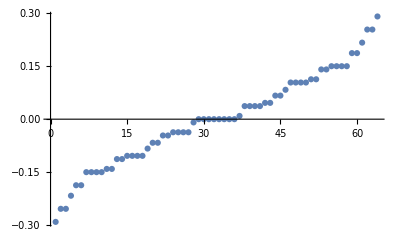

```mathematica
num=6;mass=0;a=1;g=0;t=0;t0=0;
{ε,ψ}=Eigensystem[HamSchwBos[num,t,t0,mass,a,g]]//N;
{ε,ψ}={ε[[#]]/num,Normalize/@ψ[[#]]}&@Ordering[ε]
ListPlot[ε]
```

```mathematica
num=8;mass=0;a=1;g=0;t=0;t0=0;
Eigenvalues[HamSchwBos[num,t,t0,mass,a,g],1]/num//N
```

{-0.297423}

```mathematica
LowestEigs=Table[Eigenvalues[HamSchwBos[i,0,0,0,1.0,0]/i,1],{i,2,12}]
```

Sum::itraw: Raw object 11 cannot be used as an iterator.

Sum::vloc: The variable 11 cannot be localized so that it can be assigned to numerical values.

Sum::itraw: Raw object 11 cannot be used as an iterator.

Sum::vloc: The variable 11 cannot be localized so that it can be assigned to numerical values.

Sum::itraw: Raw object 11 cannot be used as an iterator.

General::stop: Further output of Sum::itraw will be suppressed during this calculation.

Sum::vloc: The variable 11 cannot be localized so that it can be assigned to numerical values.

General::stop: Further output of Sum::vloc will be suppressed during this calculation.

{{-0.25},{-0.235702},{0.279508},{-0.273205},{-0.291163},{-0.287667},{-0.297423},{-0.295208},{-0.301334},{-0.299807},{0.30401}}

Theoretical value for the ground state energy density for the free, massless case is E_0/N=-1/π=-0.318309...

```mathematica
Flatten[LowestEigs]
```

{-0.25,-0.235702,0.279508,-0.273205,-0.291163,-0.287667,-0.297423,-0.295208,-0.301334,-0.299807,0.30401}

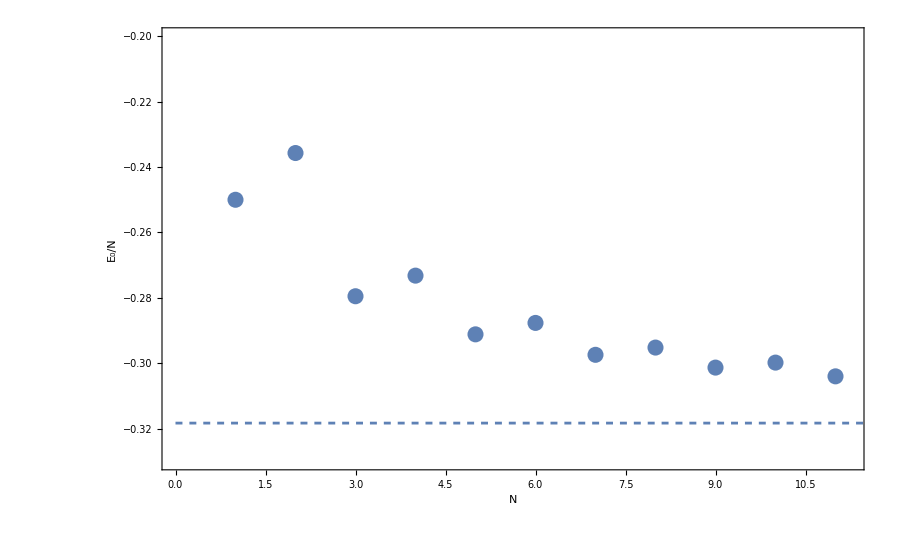

```mathematica
GroundStateEnergyDensity=Show[Plot[-1/π,{x,0,12},PlotStyle->Dashed,PlotRange->{{0,11.25},{-0.33,-0.2}}],ListPlot[{-0.25,-0.23570226039551584,-0.27950849718747367,-0.27320508075688776,-0.29116326728624475,-0.28766710658041794,-0.297423155196478,-0.29520841748194715,-0.3013337091666139,-0.2998070051238717,-0.3040095754399496}],Frame->True,Options[G2D],FrameLabel->{"N","E_0/N"}]
```

```mathematica
Export[NotebookDirectory[]<>"GroundStateEnergyDensity.pdf",GroundStateEnergyDensity]
```

/Users/cameron/Library/CloudStorage/Dropbox-HalfWheel/Cameron Cogburn/Spin-Boson Model/RPI-BNL-Schwinger/Mathematica/GroundStateEnergyDensity.pdf

#### Free massless theory

```mathematica
G2D=Graphics[{},AlignmentPoint->Center,Axes->False,AxesLabel->None,BaseStyle->{FontFamily->"Times",FontSize->22,FontColor->Black},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black],FrameTicks->True,FrameTicksStyle->Directive[24,Black](*,ImagePadding->{{20,5},{15,5}}*),ImageSize->900];
```

```mathematica
num=6;mass=0;a=1;g=0;t=0;t0=0;
{ε,ψ}=Eigensystem[HamSchwBos[num,t,t0,mass,a,g]]//N;
{ε,ψ}={ε[[#]]/num,Normalize/@ψ[[#]]}&@Ordering[ε]
ListPlot[ε]
```

-Graphics-

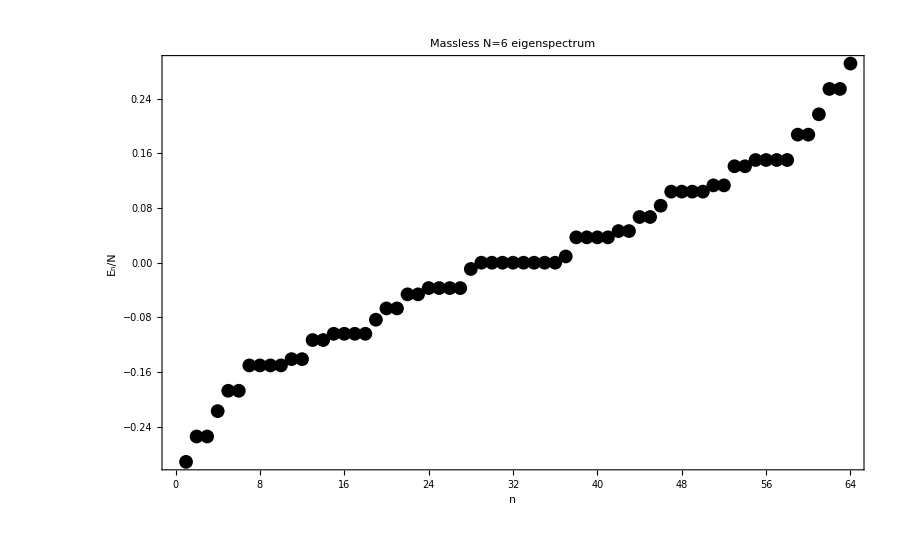

```mathematica
masslesseig6=Show[ListPlot[ε,PlotStyle->{Black},PlotLabel->"Massless N=6 eigenspectrum",LabelStyle->Directive[Black,22]],Frame->True,Options[G2D],FrameLabel->{"n","E_n/N"}]
```

```mathematica
Export[NotebookDirectory[]<>"masslesseig6.pdf",masslesseig]
```

/Users/cameron/Library/CloudStorage/Dropbox-HalfWheel/Cameron Cogburn/Spin-Boson Model/RPI-BNL-Schwinger/Mathematica/masslesseig6.pdf

```mathematica
mass=2.0;
LowestEigsMassive=Table[Eigenvalues[HamSchwBos[i,0,0,mass,1.0,0]/(mass*i),1],{i,2,9}]
```

{{-0.515388},{-0.686887},{-0.522645},{-0.6241},{0.52507},{-0.597192},{0.526283},{-0.582242}}

```mathematica
√(1/0.005)
```

14.1421

```mathematica
mass=2.0;num=7;
Eigenvalues[HamSchw[num,0,0,mass,1.0,0]/(mass*num),4]
```

{-0.597192,0.454334,-0.454334,-0.451743}

To compare with the direct solution we need to bin and normalize

### Scratch

0.3

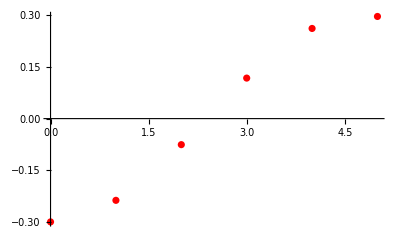

```mathematica
norm=0.3
directsol=ListPlot[Table[{1.59n,-Cos[(π*(2n+0))/6]*norm},{n,0,π,π/5.}],PlotStyle->Red]
```

```mathematica
π/5.
```

0.523599

```mathematica
num=6;mass=0;a=1;g=0;t=0;t0=0;
{ε,ψ}=Eigensystem[HamSchwBos[num,t,t0,mass,a,g]]//N;
{ε,ψ}={ε[[#]]/num,Normalize/@ψ[[#]]}&@Ordering[ε]
discretesol=ListPlot[ε]
```

-Graphics-

```mathematica
ListPlot[ε]
```

-Graphics-

```mathematica
ε
BinLists[ε,1/8.]
Table[Last /@ Flatten[%[[k]],1]//Mean,{k,1,Length@%}]
```

{-0.291163,-0.254076,-0.254076,-0.21699,-0.187248,-0.187248,-0.150161,-0.150161,-0.150161,-0.150161,-0.141002,-0.141002,-0.113075,-0.113075,-0.103915,-0.103915,-0.103915,-0.103915,-0.0833333,-0.0668281,-0.0668281,-0.0462465,-0.0462465,-0.0370868,-0.0370868,-0.0370868,-0.0370868,-0.00915969,0.,0.,0.,0.,0.,0.,0.,0.,0.00915969,0.0370868,0.0370868,0.0370868,0.0370868,0.0462465,0.0462465,0.0668281,0.0668281,0.0833333,0.103915,0.103915,0.103915,0.103915,0.113075,0.113075,0.141002,0.141002,0.150161,0.150161,0.150161,0.150161,0.187248,0.187248,0.21699,0.254076,0.254076,0.291163}

{{-0.291163,-0.254076,-0.254076},{-0.21699,-0.187248,-0.187248,-0.150161,-0.150161,-0.150161,-0.150161,-0.141002,-0.141002},{-0.113075,-0.113075,-0.103915,-0.103915,-0.103915,-0.103915,-0.0833333,-0.0668281,-0.0668281,-0.0462465,-0.0462465,-0.0370868,-0.0370868,-0.0370868,-0.0370868,-0.00915969},{0.,0.,0.,0.,0.,0.,0.,0.,0.00915969,0.0370868,0.0370868,0.0370868,0.0370868,0.0462465,0.0462465,0.0668281,0.0668281,0.0833333,0.103915,0.103915,0.103915,0.103915,0.113075,0.113075},{0.141002,0.141002,0.150161,0.150161,0.150161,0.150161,0.187248,0.187248,0.21699},{0.254076,0.254076,0.291163}}

Last::normal: Nonatomic expression expected at position 1 in Last[-0.291163].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.254076].

General::stop: Further output of Last::normal will be suppressed during this calculation.

{1/3 (Last[-0.291163]+2 Last[-0.254076]),1/9 (Last[-0.21699]+2 Last[-0.187248]+4 Last[-0.150161]+2 Last[-0.141002]),1/16 (2 Last[-0.113075]+4 Last[-0.103915]+Last[-0.0833333]+2 Last[-0.0668281]+2 Last[-0.0462465]+4 Last[-0.0370868]+Last[-0.00915969]),1/24 (8 Last[0.]+Last[0.00915969]+4 Last[0.0370868]+2 Last[0.0462465]+2 Last[0.0668281]+Last[0.0833333]+4 Last[0.103915]+2 Last[0.113075]),1/9 (2 Last[0.141002]+4 Last[0.150161]+2 Last[0.187248]+Last[0.21699]),1/3 (2 Last[0.254076]+Last[0.291163])}

```mathematica
binAndMean[xdata_List,ydata_List,nbins_Integer]:=Module[{xbins,bins},xbins=Array[#&,nbins+1,{Min@xdata,Max@xdata}];
bins=BinLists[Transpose[{xdata,ydata}],{xbins},{{-Infinity,+Infinity}}];
Table[Last/@Flatten[bins[[k]],1]//Mean,{k,1,Length@bins}]]
```

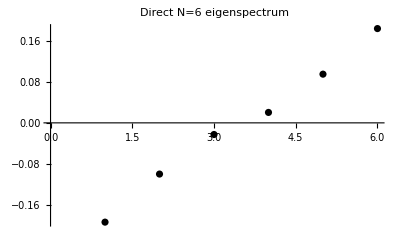

```mathematica
discretesolbin=ListPlot[Thread[binAndMean[Table[i,{i,1,Length[ε]}],ε,6]],PlotLabel->"Direct N=6 eigenspectrum",LabelStyle->Directive[Black,22],PlotStyle->Black]
```

{{0,-0.193859},{1,-0.0999801},{2,-0.0227273},{3,0.0203753},{4,0.0950952},{5,0.184129}}

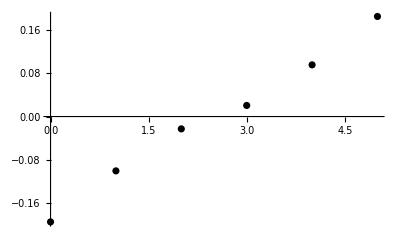

```mathematica
Thread[{{0,1,2,3,4,5},binAndMean[Table[i,{i,1,Length[ε]}],ε,6]}]
discretesolbin=ListPlot[Thread[{{0,1,2,3,4,5},binAndMean[Table[i,{i,1,Length[ε]}],ε,6]}],PlotStyle->Black]
```

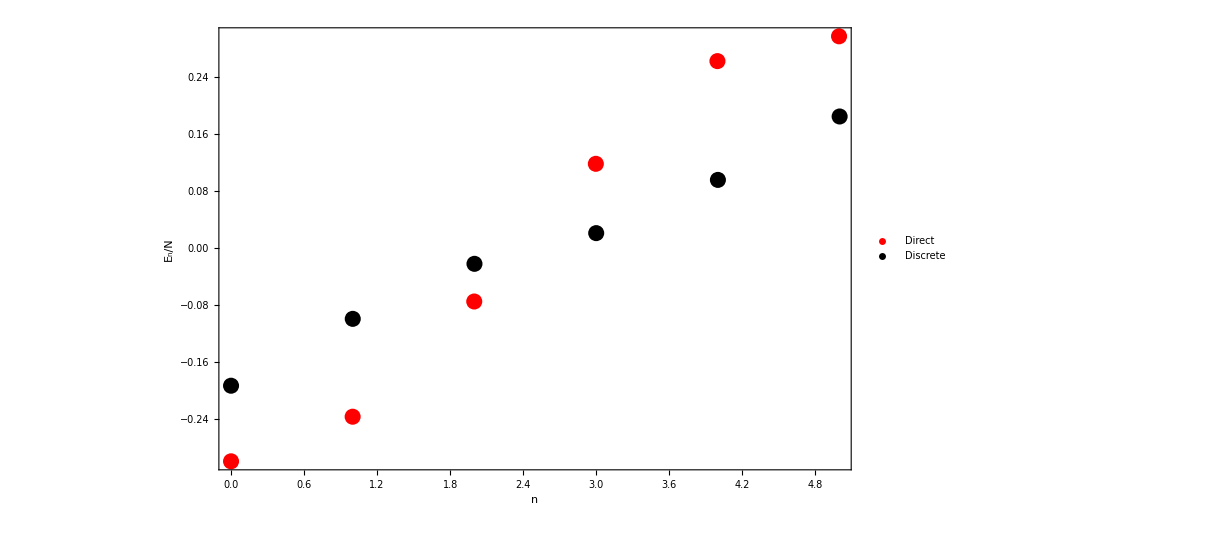

```mathematica
masslesseigenspectrumcompare6bin=Show[ListPlot[Table[{1.59n,-Cos[(π*(2n+0))/6]*norm},{n,0,π,π/5.}],LabelStyle->Directive[Black,22],PlotStyle->Red,PlotLegends->{"Direct"}],ListPlot[Thread[{{0,1,2,3,4,5},binAndMean[Table[i,{i,1,Length[ε]}],ε,6]}],LabelStyle->Directive[Black,22],PlotStyle->Black,PlotLegends->{"Discrete"}],Frame->True,Options[G2D],FrameLabel->{"n","E_n/N"}]
```

```mathematica
Export[NotebookDirectory[]<>"masslesseigenspectrumcompare6bin.pdf",masslesseigenspectrumcompare6bin]
```

/Users/cameron/Library/CloudStorage/Dropbox-HalfWheel/Cameron Cogburn/Spin-Boson Model/RPI-BNL-Schwinger/Mathematica/masslesseigenspectrumcompare6bin.pdf

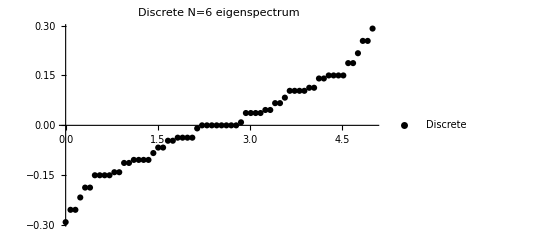

```mathematica
discretenobin=ListPlot[Thread[{Range[0,5,0.07936507936507936],ε}],PlotLabel->"Discrete N=6 eigenspectrum",LabelStyle->Directive[Black,22],PlotStyle->Black,PlotLegends->{"Discrete"}]
```

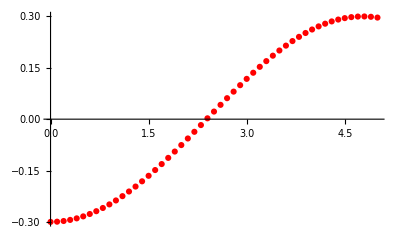

```mathematica
ListPlot[Table[{1.59n,-Cos[(π*(2n+0))/6]*norm},{n,0,π,π/50.}],PlotStyle->Red]
```

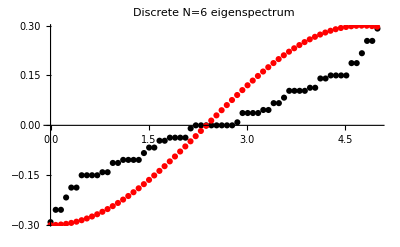

```mathematica
Show[discretenobin,ListPlot[Table[{1.59n,-Cos[(π*(2n+0))/6]*norm},{n,0,π,π/63.}],PlotStyle->Red]]
```

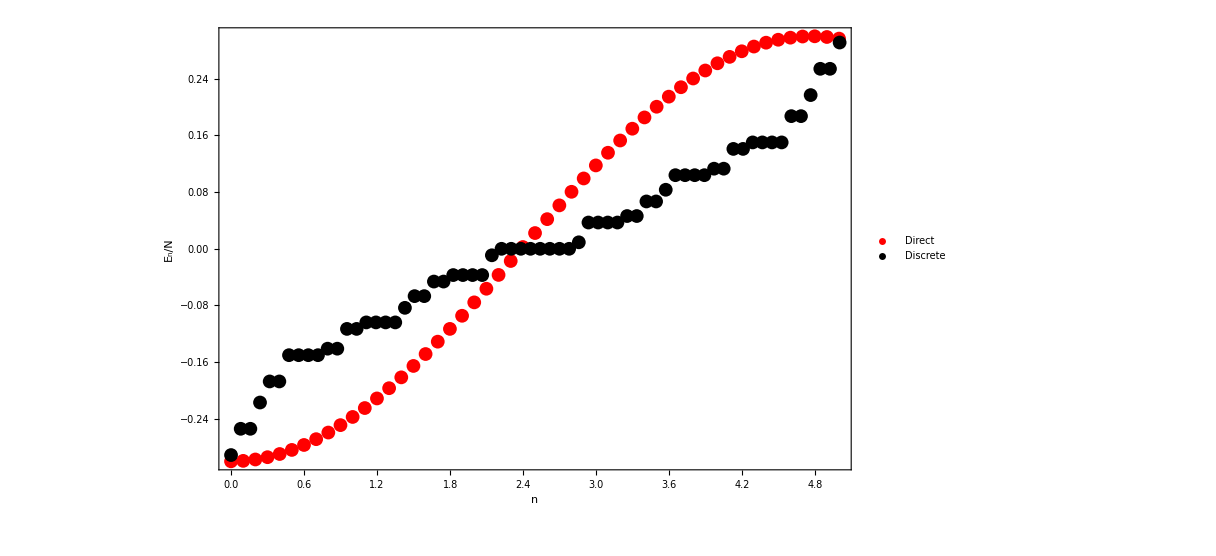

```mathematica
masslesseigenspectrumcompare6=Show[ListPlot[Table[{1.59n,-Cos[(π*(2n+0))/6]*norm},{n,0,π,π/50.}],PlotStyle->Red,PlotLegends->{"Direct"},LabelStyle->Directive[Black,22]],ListPlot[Thread[{Range[0,5,0.07936507936507936],ε}],PlotLabel->"Discrete N=6 eigenspectrum",LabelStyle->Directive[Black,22],PlotStyle->Black,PlotLegends->{"Discrete"}],Frame->True,Options[G2D],FrameLabel->{"n","E_n/N"}]
```

```mathematica
Export[NotebookDirectory[]<>"masslesseigenspectrumcompare6.pdf",masslesseigenspectrumcompare6]
```

/Users/cameron/Library/CloudStorage/Dropbox-HalfWheel/Cameron Cogburn/Spin-Boson Model/RPI-BNL-Schwinger/Mathematica/masslesseigenspectrumcompare6.pdf

```mathematica
ε
```

{-0.291163,-0.254076,-0.254076,-0.21699,-0.187248,-0.187248,-0.150161,-0.150161,-0.150161,-0.150161,-0.141002,-0.141002,-0.113075,-0.113075,-0.103915,-0.103915,-0.103915,-0.103915,-0.0833333,-0.0668281,-0.0668281,-0.0462465,-0.0462465,-0.0370868,-0.0370868,-0.0370868,-0.0370868,-0.00915969,0.,0.,0.,0.,0.,0.,0.,0.,0.00915969,0.0370868,0.0370868,0.0370868,0.0370868,0.0462465,0.0462465,0.0668281,0.0668281,0.0833333,0.103915,0.103915,0.103915,0.103915,0.113075,0.113075,0.141002,0.141002,0.150161,0.150161,0.150161,0.150161,0.187248,0.187248,0.21699,0.254076,0.254076,0.291163}

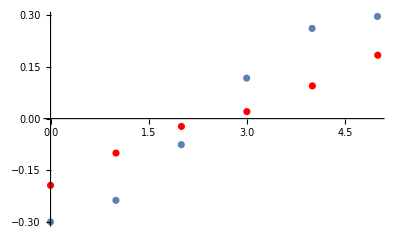

```mathematica
Show[directsol,discretesolbin]
```

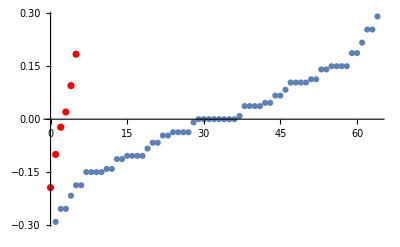

```mathematica
Show[ListPlot[ε],discretesolbin]
```

```mathematica
ε//Length
```

64

```mathematica
Table[i,{i,1,Length[ε]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

```mathematica
binAndMean[Table[i,{i,1,Length[ε]}],ε,6]
```

{-0.193859,-0.0999801,-0.0227273,0.0203753,0.0950952,0.184129}

Show::gcomb: Could not combine the graphics objects in Show[,{-0.193859,-0.0999801,-0.0227273,0.0203753,0.0950952,0.184129}].

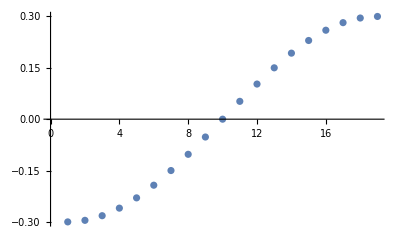
Show[-Graphics-,{-0.193859,-0.0999801,-0.0227273,0.0203753,0.0950952,0.184129}]

```mathematica
Show[directsol,binAndMean[Table[i,{i,1,Length[ε]}],ε,6]]
```

```mathematica
π/64.
```

0.0490874

```mathematica
χd[N_,n_]:=χd[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,0},{1,0}}, If[OddQ[n]==True,ArrayFlatten[TensorProduct[{{1,0},{0,-1}},IdentityMatrix[2^(N-n-1)]]],IdentityMatrix[2^(N-n)]]]],2]]
```

```mathematica
IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
ArrayFlatten[ArrayFlatten[TensorProduct[{{a1,0},{0,b1}},{{0,0},{1,0}},{{c1,0},{0,d1}}]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a1 c1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a1 d1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | b1 c1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | b1 d1 | 0 | 0)

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {a1 c1, 0, 0, 0, 0, 0, 0, 0}, {0, a1 d1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b1 c1, 0, 0, 0}, {0, 0, 0, 0, 0, b1 d1, 0, 0}})
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{a1 c1,0,0,0,0,0,0,0},{0,a1 d1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,b1 c1,0,0,0},{0,0,0,0,0,b1 d1,0,0}}

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}})
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,1,0,0}}

```mathematica
Solve[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{a1 c1,0,0,0,0,0,0,0},{0,a1 d1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,b1 c1,0,0,0},{0,0,0,0,0,b1 d1,0,0}}=={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,1,0,0}},{a1,b1,c1,d1}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b1→-a1,c1→1/a1,d1→-1/a1}}

```mathematica
b1=ArrayFlatten[ArrayFlatten[TensorProduct[{{0,0},{1,0}},{{1,0},{0,1}},{{1,0},{0,1}}]]];
b2=ArrayFlatten[ArrayFlatten[TensorProduct[{{1,0},{0,-1}},{{0,0},{1,0}},{{1,0},{0,1}}]]];
b3=ArrayFlatten[ArrayFlatten[TensorProduct[{{-1,0},{0,1}},{{-1,0},{0,1}},{{0,0},{1,0}}]]];
b1//MatrixForm
b2//MatrixForm
b3//MatrixForm
b1.b2+b2.b1//MatrixForm
b1.b3+b3.b1//MatrixForm
b2.b3+b3.b2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
b1=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}});
b2=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 0, 0}});
b3=({{0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
b1.b2+b2.b1//MatrixForm
b1.b3+b3.b1//MatrixForm
b2.b3+b3.b2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
b3//MatrixForm
ajb3=SparseArray[b3]["AdjacencyLists"]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

{{},{1},{},{3},{},{5},{},{7}}

```mathematica
First/@SequencePosition[#,{Except[0]}]&/@b3
```

{{},{1},{},{3},{},{5},{},{7}}

```mathematica
BaseForm[7,2]
```

111_2

```mathematica
DigitCount[7,2,1]
```

3

```mathematica
ConstantArray[0,Length[ajb3]]
```

{0,0,0,0,0,0,0,0}

```mathematica
Flatten[Table[(-1)^DigitCount[ajb3[[i]]-1,2,1](*ajb3[[i]]*),{i,1,Length[ajb3]}]/.{}->{0}]+ConstantArray[0,Length[ajb3]]
```

{0,1,0,-1,0,-1,0,1}

```mathematica
Flatten[Table[(-1)^DigitCount[ajb1[[i]]-1,2,1](*ajb3[[i]]*),{i,1,Length[ajb1]}]/.{}->{0}]+ConstantArray[0,Length[ajb1]]
```

{0,0,0,0,1,-1,-1,1}

```mathematica
MatrixForm[ajb3]
```

({}
{1}
{}
{3}
{}
{5}
{}
{7})

```mathematica
SparseArray[b3]
```

SparseArray[…]

```mathematica
Clear[list,r]
(*list={{1,4,2,11,4,72},{2,14,4,20},{},{1,54,2,16,3,15},{3,99}};*)
list={{},{1},{},{3},{},{5},{},{7}}
r=Join@@ReplacePart[list,i_:>SequenceCases[list[[i]],{a_,b_}:>{i,a}->(-1)^DigitCount[list[[i]]-0,2,1] a]]
```

{{},{1},{},{3},{},{5},{},{7}}

{}

```mathematica
ReplacePart[#1,#2->x]&,{a,b,c,d,e},{5,2,3,1,4}]
```

```mathematica
ReplacePart[b3,{i_,j_}:>(-1)^DigitCount[b3[[i,j]]-1,2,1] b3[[i,j]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
b1=ArrayFlatten[ArrayFlatten[TensorProduct[{{0,0},{1,0}},{{1,0},{0,1}},{{1,0},{0,1}}]]];
b2=ArrayFlatten[ArrayFlatten[TensorProduct[{{1,0},{0,1}},{{0,0},{1,0}},{{1,0},{0,1}}]]];
b3=ArrayFlatten[ArrayFlatten[TensorProduct[{{1,0},{0,1}},{{1,0},{0,1}},{{0,0},{1,0}}]]];
```

```mathematica
SparseArray[b1]["AdjacencyLists"]
```

{{},{},{},{},{1},{2},{3},{4}}

```mathematica
(-1)^DigitCount[SparseArray[b1]["AdjacencyLists"][[5]]-1,2,1]
```

{1}

```mathematica
ajb1(*/.{}->{0}*)
Table[DigitCount[%[[i]]-1,2,1],{i,1,Length[ajb1]}]/.{}->{0}
```

{{},{},{},{},{1},{2},{3},{4}}

{{0},{0},{0},{0},{0},{1},{1},{2}}

```mathematica
ajb2+ConstantArray[{0},8]
```

Thread::tdlen: Objects of unequal length in {}+{0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{}+{0},{}+{0},{1},{2},{}+{0},{}+{0},{5},{6}}

```mathematica
IntegerDigits[0,2]
```

{0}

0

```mathematica
FromDigits/@StringSplit[IntegerString[0,2,3],3]
```

StringExpression::invld: Element 3 is not a valid string or pattern element in 3.

FromDigits::nlst: The expression 3 is not a list of digits or a string of valid digits.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[0,FromDigits[3]].

StringSplit[0,FromDigits[3]]

```mathematica
ajb1/.{}->{0}
Table[IntegerDigits[%[[i]]-1,2][[1]],{i,1,8}]
```

{{0},{0},{0},{0},{1},{2},{3},{4}}

{{1},{1},{1},{1},{0},{1},{1,0},{1,1}}

```mathematica
BaseForm[ajb2[[8]]-1,2]
IntegerDigits[ajb2[[8]]-1,2][[1]]
Sum[%[[i]],{i,2,Length[%]}]
Sum[IntegerDigits[ajb2[[8]]-1,2][[1]][[i]],{i,2,Length[IntegerDigits[ajb2[[8]]-1,2][[1]]]}]
(*DigitCount[ajb2[[7]]-1,2,1]*)
```

{101_2}

{1,0,1}

1

1

```mathematica
Table[Sum[IntegerDigits[ajb2[[j]]-1,2][[1]][[i]],{i,2,Length[IntegerDigits[ajb2[[8]]-1,2][[1]]]}],{j,1,8}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1+{}⟦1⟧⟦3⟧,1+{}⟦1⟧⟦3⟧,{0}⟦2⟧+{0}⟦3⟧,{1}⟦2⟧+{1}⟦3⟧,1+{}⟦1⟧⟦3⟧,1+{}⟦1⟧⟦3⟧,0,1}

```mathematica
ajb1
ConstantArray[{0},8]
```

{{},{},{},{},{1},{2},{3},{4}}

{{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
ajb1+ConstantArray[{0},8]
```

Thread::tdlen: Objects of unequal length in {}+{0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{}+{0},{}+{0},{}+{0},{}+{0},{1},{2},{3},{4}}

```mathematica
Table[Total[IntegerDigits[ajb1[[i]],2][[1]]],{i,2,8}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{Total[{}⟦1⟧],Total[{}⟦1⟧],Total[{}⟦1⟧],1,1,2,1}

```mathematica
Table[Total[IntegerDigits[ajb1[[i]],2][[1]]],{i,1,8}]
Table[Sum[IntegerDigits[ajb2[[i]],2][[1]][[j]],{j,1,Length[ajb2[[i]]]}],{i,1,8}]
Table[Sum[IntegerDigits[ajb3[[i]],2][[1]][[j]],{j,1,Length[ajb3[[i]]]}],{i,1,8}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{Total[{}⟦1⟧],Total[{}⟦1⟧],Total[{}⟦1⟧],Total[{}⟦1⟧],1,1,2,1}

{0,0,1,1,0,0,1,1}

{0,1,0,1,0,1,0,1}

```mathematica
Clear[ajb1,ajb2,ajb3,templist1,templist2,templist3]
ajb1=SparseArray[b1]["AdjacencyLists"]
ajb2=SparseArray[b2]["AdjacencyLists"]
ajb3=SparseArray[b3]["AdjacencyLists"]
(*templist1=Flatten[Table[(-1)^DigitCount[ajb1[[i]]-1,2,1](*ajb3[[i]]*),{i,1,2^1-1}]/.{}->{0}](*+ConstantArray[0,Length[ajb1]]*)*)
templist1=Flatten[Table[(-1)^Sum[IntegerDigits[ajb1[[i]]-1,2][[1]][[j]],{j,1,Length[ajb1[[i]]]}](*ajb3[[i]]*),{i,1,2^1-1}]/.{}->{0}](*+ConstantArray[0,Length[ajb1]]*)
templist2=Flatten[Table[(-1)^DigitCount[ajb2[[i]]-1,2,1](*ajb3[[i]]*),{i,1,2^2-1(*Length[ajb2]*)}]/.{}->{0}](*+ConstantArray[0,Length[ajb2]]*)
templist3=Flatten[Table[(-1)^DigitCount[ajb3[[i]]-1,2,1](*ajb3[[i]]*),{i,1,2^3-1(*Length[ajb3]*)}]/.{}->{0}](*+ConstantArray[0,Length[ajb3]]*)
```

{{},{},{},{},{1},{2},{3},{4}}

{{},{},{1},{2},{},{},{5},{6}}

{{},{1},{},{3},{},{5},{},{7}}

{1}

{0,0,1}

{0,1,0,-1,0,-1,0}

```mathematica
DigitCount[ajb1[[8]]-1,2,1]
```

{2}

```mathematica
ReplacePart[b1,{i_,j_}:>(*templist[[j]]**)templist1[[i]]*b1[[i,j]]]//MatrixForm
ReplacePart[b2,{i_,j_}:>(*(-1)^DigitCount[b2[[i,j]]+1,2,1]*)templist2[[i]]*b2[[i,j]]]//MatrixForm
ReplacePart[b3,{i_,j_}:>(*(-1)^DigitCount[b3[[i,j]]-1,2,1]*)templist3[[i]]*b3[[i,j]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
IntegerDigits[0,2]
```

{0}

```mathematica
IntegerString[0,2,3]
Characters@%
```

000

{0,0,0}

```mathematica
IntegerString[7,2,3]
Characters@%
```

111

{1,1,1}

```mathematica
ajb1=SparseArray[b1]["AdjacencyLists"]
ajb1/.{}->{0}
ToExpression[Table[Characters@IntegerString[%[[i]]-1,2,3][[1]],{i,1,8}]]
Table[Sum[%[[i]][[j]],{j,1,1}],{i,1,8}]
Table[(-1)^(%[[i]]),{i,1,8}]
```

{{},{},{},{},{1},{2},{3},{4}}

{{0},{0},{0},{0},{1},{2},{3},{4}}

{{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,0},{0,0,1},{0,1,0},{0,1,1}}

{0,0,0,0,0,0,0,0}

{1,1,1,1,1,1,1,1}

```mathematica
ajb2=SparseArray[b2]["AdjacencyLists"]
ajb2/.{}->{0}
ToExpression[Table[Characters@IntegerString[%[[i]]-1,2,3][[1]],{i,1,8}]]
Table[Sum[%[[i]][[j]],{j,1,2}],{i,1,8}]
Table[(-1)^(%[[i]]),{i,1,8}]
```

{{},{},{1},{2},{},{},{5},{6}}

{{0},{0},{1},{2},{0},{0},{5},{6}}

{{0,0,1},{0,0,1},{0,0,0},{0,0,1},{0,0,1},{0,0,1},{1,0,0},{1,0,1}}

{0,0,0,0,0,0,1,1}

{1,1,1,1,1,1,-1,-1}

```mathematica
ajb3=SparseArray[b3]["AdjacencyLists"]
ajb3/.{}->{0}
ToExpression[Table[Characters@IntegerString[%[[i]]-1,2,3][[1]],{i,1,8}]]
Table[Sum[%[[i]][[j]],{j,1,3}],{i,1,8}]
Table[(-1)^(%[[i]]),{i,1,8}]
```

{{0},{1},{0},{3},{0},{5},{0},{7}}

{{0,0,1},{0,0,0},{0,0,1},{0,1,0},{0,0,1},{1,0,0},{0,0,1},{1,1,0}}

{1,0,1,1,1,1,1,2}

{-1,1,-1,-1,-1,-1,-1,1}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0}}

```mathematica
b3//MatrixForm
ajb3=SparseArray[b3]["AdjacencyLists"]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

{{},{1},{},{3},{},{5},{},{7}}

```mathematica
ajb3zeros=ajb3/.{}->{0}
ToExpression[Table[Characters@IntegerString[%[[i]]-1,2,3][[1]],{i,1,8}]]
Table[Sum[%[[i]][[j]],{j,1,3}],{i,1,8}]
tempans=Table[(-1)^(%[[i]]),{i,1,8}]
```

{{0},{1},{0},{3},{0},{5},{0},{7}}

{{0,0,1},{0,0,0},{0,0,1},{0,1,0},{0,0,1},{1,0,0},{0,0,1},{1,1,0}}

{1,0,1,1,1,1,1,2}

{-1,1,-1,-1,-1,-1,-1,1}

```mathematica
b3
```

{{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0}}

```mathematica
ajb1zeros=ajb1/.{}->{0};
ToExpression[Table[Characters@IntegerString[%[[i]]-1,2,3][[1]],{i,1,8}]];
Table[Sum[%[[i]][[j]],{j,1,1}],{i,1,8}];
tempans1=Table[(-1)^(%[[i]]),{i,1,8}];
Table[b1[[i,j]]*tempans1[[i]],{i,1,8},{j,1,8}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
ajb2zeros=ajb2/.{}->{0};
ToExpression[Table[Characters@IntegerString[%[[i]]-1,2,3][[1]],{i,1,8}]];
Table[Sum[%[[i]][[j]],{j,1,2}],{i,1,8}];
tempans2=Table[(-1)^(%[[i]]),{i,1,8}];
Table[b2[[i,j]]*tempans2[[i]],{i,1,8},{j,1,8}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)

```mathematica
ajb3=SparseArray[b3]["AdjacencyLists"]
ajb3zeros=ajb3/.{}->{0};
ToExpression[Table[Characters@IntegerString[%[[i]]-1,2,3][[1]],{i,1,8}]];
Table[Sum[%[[i]][[j]],{j,1,3}],{i,1,8}];
tempans3=Table[(-1)^(%[[i]]),{i,1,8}];
Table[b3[[i,j]]*tempans3[[i]],{i,1,8},{j,1,8}]//MatrixForm
```

{{},{1},{},{3},{},{5},{},{7}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

Create fermionic creation/annihilation operators correctly once and for all.

```mathematica
Clear[χ,χd,tempχd,adj,adjzeros,toexpr,table,tempans]
(*χ[N0_,n0_]:=Module[{N=N0,n=n0},
tempχd=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,1},{0,0}}, IdentityMatrix[2^(N-n)]]],2]];
adj=SparseArray[tempχd]["AdjacencyLists"];
adjzeros=adj/.{}->0;
toexpr=ToExpression[Table[Characters@IntegerString[adjzeros[[i]]-1,2,N][[1]],{i,1,2^N}]]//Quiet;
table=Table[Sum[toexpr[[i]][[j]],{j,1,n}],{i,1,2^N}]//Quiet;
tempans=Table[(-1)^table[[i]],{i,1,2^N}];
Table[tempχd[[i,j]]*tempans[[i]],{i,1,2^N},{j,1,2^N}]]*)
χd[N0_,n0_]:=Module[{N=N0,n=n0},
tempχd=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,0},{1,0}}, IdentityMatrix[2^(N-n)]]],2]];
adj=SparseArray[tempχd]["AdjacencyLists"];
adjzeros=adj/.{}->0;
toexpr=ToExpression[Table[Characters@IntegerString[adjzeros[[i]]-1,2,N][[1]],{i,1,2^N}]]//Quiet;
table=Table[Sum[toexpr[[i]][[j]],{j,1,n}],{i,1,2^N}]//Quiet;
tempans=Table[(-1)^table[[i]],{i,1,2^N}];
Table[tempχd[[i,j]]*tempans[[i]],{i,1,2^N},{j,1,2^N}]]
χ[N0_,n0_]:=χ[N0,n0]=ConjugateTranspose[χd[N0,n0]]
```

```mathematica
χd[2,2]//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1 | 0)

```mathematica
AntiCommutator[χ[2,1],χ[2,1]]//MatrixForm
AntiCommutator[χ[2,1],χd[2,1]]//MatrixForm
AntiCommutator[χd[2,1],χd[2,2]]//MatrixForm
AntiCommutator[χd[2,1],χ[2,2]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
χd[4,4]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
AntiCommutator[χ[3,1],χd[3,1]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
χ[3,1].χd[3,1]//MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
χd[3,1]//MatrixForm
ConjugateTranspose[χd[3,1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
AntiCommutator[χ[3,1],χ[3,1]]//MatrixForm
AntiCommutator[χ[3,1],χd[3,1]]//MatrixForm
AntiCommutator[χd[3,1],χd[3,2]]//MatrixForm
AntiCommutator[χd[3,1],χ[3,2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Clear[χ,χd]
χ[N_,n_]:=χ[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,1},{0,0}}, If[OddQ[n]==True,ArrayFlatten[TensorProduct[{{1,0},{0,-1}},IdentityMatrix[2^(N-n-1)]]],IdentityMatrix[2^(N-n)]]]],2]]
χd[N_,n_]:=χd[N,n]=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,0},{1,0}}, If[OddQ[n]==True,ArrayFlatten[TensorProduct[{{1,0},{0,-1}},IdentityMatrix[2^(N-n-1)]]],IdentityMatrix[2^(N-n)]]]],2]]*)
```

## Measuring the Charges

Now that we have the Hamiltonian and have done some basic checks, let’s see if we can measure the charges of the system. In particular, we aim to reproduce Figure 4 of Florio and Kharzheev (2404.00087). 
To do this, we need to find the “Schmidt vectors” of the system. This goes as follows. Time evolution of the vacuum state is given by:
																			|Ψ_t> = T exp(-i (∫_0)^t dt' H(t'))|Ψ_0> 
If we want to study, say, the entanglement between the left and right half of the lattice, we partition the Hilbert space as
													H=H_L⊗ H_R
We can then define the density matrix and do a Schmidt decomposition on it:
										ρ(t) =|Ψ_t><Ψ_t|= ∑_(i=1)^(2^(N/2)) λ_i(t)|ψ_i(t)><ψ_i(t) |
where
 											|ψ_i(t)> = |ψ_i^L(t)> ⊗|ψ_i^R(t)> 
 and the states |ψ_i^(L/R)(t)> are the Schmidt vectors.
 
 Clearly the total charge Q=∑_(n=1)^N q_n of the system is conserved. If starting with the vacuum state, where Q=0, this will stay so under time evolution. However, individual Schmidt vectors can have a certain charge as well that can be non-zero, so long as the sum Q_L+Q_R=0, where
																		 ∑_(n=1)^(N/2) q_n|ψ_i^(L/R)> = Q_(L/R)|ψ_i^(L/R)> 
So to verify Figure 4 of 2404.00087 we first need to find the Schmidt vectors to then measure the charge.

## Definition

```mathematica
ClearAll[MatrixPartialTrace]
SyntaxInformation[MatrixPartialTrace] = {"ArgumentsPattern" -> {_, _, __}};
Options[MatrixPartialTrace]={Method->Automatic,"Verbose"->False};
(*Attributes[MatrixPartialTrace]={};*)
MatrixPartialTrace::usage="Compute a partial trace of a matrix.";
```

```mathematica
MatrixPartialTrace::notmat="The first argument '``' has to be a square matrix.";
MatrixPartialTrace::invmeth="Invalid value '``' of the Method option.";
MatrixPartialTrace::invdim="The third argument '``' must be a positive integer or a list of positive integers.";
MatrixPartialTrace::invdimint="The value of the third argument '``', representing the input dimension, is not consistent with the dimensions '``' of the matrix in the first argument.";
MatrixPartialTrace::incdim="The product '``' of subspace dimensions '``' in the third argument must be equal to the row/column dimension '``' of the matrix in the first argument.";
MatrixPartialTrace::invidx="The second argument '``' must be a nonzero integer or a list of nonzero integers or tokens such as All, Except or Span.";
MatrixPartialTrace::largeidx="The individual indices '``' in the second argument cannot exceed the total number '``' of subspace dimensions given in the third argument.";
MatrixPartialTrace::repidx="The indices '``' in the second argument cannot repeat.";
MatrixPartialTrace::invspan="Invalid Span specification '``' in the second argument.";
MatrixPartialTrace::invexc="Invalid Except specification '``' in the second argument.";
```

```mathematica
preprocessArguments[mat_,idx_,dims_]:=Module[{lmat=mat,lidx=idx,ldims=dims,matdims,subnum},

(* --- preprocess mat --- *)

(*if mat is not a matrix and/or is not a square matrix, throw an error*)
If[(!MatrixQ[lmat])||Unequal@@(matdims=Dimensions[lmat]),
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::notmat,Shallow[lmat]];Return[$Failed]
];

(* --- preprocess dims --- *)

(*if dims is an (unevaluated) symbol, throw an error*)
If[Head[ldims]==Symbol,
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invdim,ldims];Return[$Failed]
];

(*if dims is a positive integer, try to create a list of subdimensions; it the resulting list is not valid, throw an error*)
If[IntegerQ[ldims],
If[Positive[ldims],
subnum=Log[ldims,First[matdims]];
If[!IntegerQ[subnum],
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invdimint,ldims,matdims];Return[$Failed];,
ldims=Table[ldims,subnum];
],
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invdim,ldims];Return[$Failed];
];
];

(*if dims is a list of positive integers (or the preprocessing above turned it into one), check whether the product of subdimensions gives the dimension of the input matrix and if not, throw an error; if dims is not a list of positive integers, throw an error*)
If[Head[ldims]==List&&TrueQ@AllTrue[ldims,IntegerQ[#]&&Positive[#]&],
If[Times@@ldims≠First[matdims],
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::incdim,Times@@ldims,ldims,First@matdims];Return[$Failed];,
subnum=Length[ldims];
];
,ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invdim,ldims];Return[$Failed];
];

(* --- preprocess idx --- *)

(*if idx is token All, expand it into an explicit list*)
If[lidx===All,lidx=Range[subnum]];

(*if idx is an integer, turn it into a list*)
If[IntegerQ[lidx],lidx={lidx}];

(*if idx is token Except, convert it into a list; if the resulting list is not valid, throw an error*)
If[Head[lidx]===Except,
lidx=List@@lidx;
If[MatchQ[lidx,{_Integer}|{{__Integer}}],
lidx=Select[Flatten[lidx],Abs[#]≤subnum&];
lidx=Complement[Range[subnum],Mod[lidx,subnum+1]];
,ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invexc,lidx];Return[$Failed];
];
];

(*if idx is token Span, convert it into a list; if the resulting list is not valid, throw an error*)
If[Head[lidx]===Span,
lidx=List@@lidx;
lidx=Quiet@Check[Range@@lidx,$Failed];
If[lidx===$Failed,ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invspan,lidx];Return[$Failed]];
];

(*if idx is not a list or the preprocessing above hasn't turned it into one, throw an error; otherwise do further preprocessing*)
If[Head[lidx]===List,

(*if idx is not empty and contains only nonzero integers, do further preprocessing; otherwise throw an error*)
If[lidx≠{},
If[TrueQ@AllTrue[lidx,IntegerQ[#]&&(#≠0)&],

(*if idx contains integers that are out of range (both in positive and negative direction), throw an error; otherwise turn negative integers/indices into positive ones in range {1,...,number of subspaces} and sort them *)
If[!AllTrue[lidx,(Abs[#]≤subnum)&],
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::largeidx,lidx,subnum];Return[$Failed]
];
lidx=Sort@Mod[lidx,subnum+1];

(*if some indices in idx repeat, throw an error*)
If[!DuplicateFreeQ[lidx],
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::repidx,lidx];Return[$Failed]
];
,ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invidx,lidx];Return[$Failed]
]];
,
ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invidx,lidx];Return[$Failed]
];

(* --- return preprocessed arguments --- *)

{lmat,lidx,ldims,matdims,subnum}
]
```

```mathematica
ptraceSum[mat_,idx_,dims_]:=Module[{aux,lmat=mat,ldims=dims,pre,d,post},

(*partial trace over individual subsystems*)
Do[
(*for a given subsystem determine the dimension etc.*)
pre=Times@@ldims[[;;subidx-1]];
d=ldims[[subidx]];
post=Times@@ldims[[subidx+1;;]];

(*the resulting matrix is computed block-wise,
each block is a sum of appropriate blocks of the original matrix*)
aux=Table[
Sum[
lmat[[
post (d(is-1)+k-1)+1;;post(d(is-1)+k),
post (d(js-1)+k-1)+1;; post(d(js-1)+k)
]]
,{k,d}]
,{is,pre},{js,pre}
];

(*from block representation into 2D matrix representation*)
lmat=ArrayFlatten[aux];

(*drop the dimension over which we just traced over as a preparation for the next step*)
ldims=Drop[ldims,{subidx}];

,{subidx,Reverse[idx]}
];

lmat
]
```

```mathematica
ptraceTensor[mat_,idx_,dims_]:=Module[{lmat=mat,lidx=idx,resdim},

(*from 2D matrix representation into high.-dim. tensor representation*)
lmat=ArrayReshape[lmat,Flatten[{dims,dims}]];

(*the actual partial trace*)
lidx=Transpose[{idx,idx+Length[dims]}];
lmat=TensorContract[lmat,lidx];

(*in the special case, when partial trace is an actual trace that returns a number, turn the number into 2D array*)
If[Length[idx]==Length[dims],lmat=If[Head[mat]===SparseArray,SparseArray[{{lmat}}],{{lmat}}]];

(*from high.-dim. representation back into the 2D matrix representation*)
resdim=(Times@@dims)/(Times@@dims[[idx]]);
lmat=ArrayReshape[lmat,{resdim,resdim}];

(*return result*)
lmat
]
```

```mathematica
MatrixPartialTrace[mat_,idx_,dims_,OptionsPattern[]]:=Module[{method=OptionValue[Method],verbose=OptionValue["Verbose"],fun,lmat=mat,lidx=idx,ldims=dims,matdims,subnum,args},
(*
inputs:
 mat - input matrix; must be a square matrix
idx - an integer or a list of integers that index subspaces to be traced over; also tokens All, Except, and Span are allowed
dims - dimensions of individual subspaces entered either as a list or as a single integer; in the latter case all subspaces are assumed to have the same dimension and their number is deduced from the matrix mat dimensions;

outputs:
 a square matrix that is equal to the partial trace of the input matrix;

options:
 Method - possible choices: "TensorContract", "Sum", Automatic; "TensorContract" uses TensorContract internally and is fast for numerical matrices; "Sum" uses Sum internally and is fast for symbolic matrices, Automatic chooses "TensorContract" when the input matric is numerical and "Sum" when it is symbolic;
"Verbose" - possible choices: True, False; If True, then the summary of preprocessed input parameters is printed (together with the result);
*)

(* --- preprocess arguments --- *)

args=preprocessArguments[mat,idx,dims];
If[args===$Failed,Return[$Failed],{lmat,lidx,ldims,matdims,subnum}=args];

(* --- preprocess options --- *)

(*choose a particular method*)
method=If[method===Automatic,
If[MatrixQ[lmat,NumberQ],"TensorContract","Sum"],
method];

(*if "Verbose" is true, print the summary of input parameters*)
If[verbose,Print[Grid[
{{Style["Summary of input parameters",Bold],SpanFromLeft},
{"matrix dimensions",matdims},
{"numeric matrix",MatrixQ[lmat,NumberQ]},
{"method",Which[lidx=={},None,lidx==Range[subnum],"Tr",True,method]},
{"number of subspaces",subnum},
{"subspace dimensions",ldims},
{"subspace indices",lidx}},
Frame->All
]]];

(* --- choose the actual function and apply it --- *)

(*when no tracing is necessary, return the input matrix*)
If[lidx=={},Return[lmat]];

(*when tracing over all subspaces, skip successive partial tracing and apply instead directly Tr*)
If[lidx==Range[subnum],Return[If[Head[mat]===SparseArray,SparseArray,Identity]@{{Tr[lmat]}}]];

(*in all other cases, choose one of the two low-level functions and apply it*)
fun=Switch[method,
"TensorContract",ptraceTensor,
"Sum",ptraceSum,
_,ResourceFunction["ResourceFunctionMessage"][MatrixPartialTrace::invmeth,method];Return[$Failed]
];
fun[lmat,lidx,ldims]
]
```

```mathematica
testvec=1/(√3){1,1,1,0}
```

{1/(√3),1/(√3),1/(√3),0}

```mathematica
Outer[Times,testvec,testvec]//MatrixForm
```

(1/3 | 1/3 | 1/3 | 0
1/3 | 1/3 | 1/3 | 0
1/3 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0)

```mathematica
fulldens=Outer[Times,testvec,testvec];
```

```mathematica
{fullevals,fullevecs}=Eigensystem[fulldens]
```

{{1,0,0,0},{{1,1,1,0},{0,0,0,1},{-1,0,1,0},{-1,1,0,0}}}

```mathematica
Transpose[ArrayReshape[Normalize[fullevecs[[1]]],{1,2}]].ArrayReshape[Normalize[fullevecs[[1]]],{1,2}]//Flatten//MatrixForm
```

(1/3
1/3
1/3
1/3)

```mathematica
ArrayFlatten[Outer[Times,{1/(√3),1/(√3),1/(√3),0},{1/(√3),1/(√3),1/(√3),0},2]]//MatrixForm
```

(1/3 | 1/3 | 1/3 | 0
1/3 | 1/3 | 1/3 | 0
1/3 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0)

```mathematica
Sum[ArrayFlatten[√fullevals*TensorProduct[ArrayReshape[Normalize[fullevecs[[i]]],{2,1}],ArrayReshape[Normalize[fullevecs[[i]]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten
```

What the code below does is takes the full density matrix and computes the reduced density matrix 
																			ρ_A =Tr_B(|Ψ_t><Ψ_t|)
From this it computes the normalized eigenvectors and eigenvalues for ρ_A. We can then write the full wavefunction as
													|Ψ>_AB=∑_(i,μ) ψ_(i,μ)|i>_A⊗|μ>_B=∑_i |i>_A⊗|i'>_B
where
													|i'> = ∑_μ ψ_(i,μ)|μ>_B
So the key pieces of information is computes is |i>_A and |i'>_B.

```mathematica
MatrixPartialTrace[Outer[Times,{1/(√3),1/(√3),1/(√3),0},{1/(√3),1/(√3),1/(√3),0}],2,{2,2}];
Eigensystem[%]//N
```

{{0.872678,0.127322},{{1.61803,1.},{-0.618034,1.}}}

```mathematica
Normalize[{1/2 (1+√5),1}]//FullSimplify//N
Normalize[{1/2 (1-√5),1}]//Simplify//N
%.%%//FullSimplify
```

{0.850651,0.525731}

{-0.525731,0.850651}

0.

```mathematica
√0.12732200375003502
```

0.356822

```mathematica
Clear[LSeV,NormLSV,RSeV,NormRSV,RSVtemp,coeffs,testWF,coeffs,temp]
SchmidtVectors[Ψ0_]:=Module[{Ψ=Ψ0},
VectorLength=Length[Ψ]/2;
FullDensityMatrix=Outer[Times,Ψ,Ψ];
ρL=MatrixPartialTrace[FullDensityMatrix,2,{VectorLength,VectorLength}];
ρR=MatrixPartialTrace[FullDensityMatrix,1,{VectorLength,VectorLength}];
{LeftEigenvalues,LeftEigenvectors}=Eigensystem[ρL];
{LeftEigenvalues,LeftEigenvectors}={LeftEigenvalues[[#]],LeftEigenvectors[[#]]}&@Ordering[LeftEigenvalues];
{RightEigenvalues,RightEigenvectors}=Eigensystem[ρR];
{RightEigenvalues,RightEigenvectors}={RightEigenvalues[[#]],RightEigenvectors[[#]]}&@Ordering[RightEigenvalues];
{LSeV,LSV,RSeV,RSV}={LeftEigenvalues,LeftEigenvectors,RightEigenvalues,RightEigenvectors};
NormLSV=Table[Normalize[LSV[[i]]],{i,1,2}]//FullSimplify;
NormRSV=Table[Normalize[RSV[[i]]],{i,1,2}]//FullSimplify;
coeffs={aa,aa*b};
testWF=Sum[ArrayFlatten[coeffs[[i]] √LSeV[[i]]*TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[NormLSV[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten;
coeffsolved=Solve[testWF==Ψ,{aa,b}]//Flatten;
temp=Table[{coeffs[[i]] √LSeV[[i]]*ArrayReshape[NormLSV[[i]],{2,1}]},{i,1,2}]/.coeffsolved//FullSimplify//Flatten;
RSVtemp=ArrayReshape[temp,{2,2}];
{LSeV,NormLSV,RSeV,NormRSV,RSVtemp}
]
```

```mathematica
{LSeV,NormLSV,RSeV,NormRSV,RSVtemp}=SchmidtVectors[{1/(√3),1/(√3),1/(√3),0}]
Sum[ArrayFlatten[TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[RSVtemp[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten//N
%.%
```

{{1/6 (3-√5),1/6 (3+√5)},{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))},{√(1/10 (5+√5)),√(2/(5+√5))}},{1/6 (3-√5),1/6 (3+√5)},{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))},{√(1/10 (5+√5)),√(2/(5+√5))}},{{√(1/15 (5-2 √5)),Root-0.304Root[1-15 #1^2+45 #1^4&,2]-0.30353099910334314},{√(1/15 (5+2 √5)),√(1/30 (5+√5))}}}

{0.57735,0.57735,0.57735,0.}

1.

```mathematica
LSeV//N
NormLSV//N
```

{0.127322,0.872678}

{{-0.525731,0.850651},{0.850651,0.525731}}

```mathematica
TensorProduct[{-0.85,-0.52},{-0.85,-0.52}]//Flatten
```

{0.7225,0.442,0.442,0.2704}

```mathematica
NormLSV
```

{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))},{√(1/10 (5+√5)),√(2/(5+√5))}}

```mathematica
coe={a1,-a1*a2};
NormLSV1=Table[coe[[i]]*NormLSV[[i]],{i,1,2}]
Sum[√LSeV[[i]] TensorProduct[NormLSV[[i]],NormLSV1[[i]]],{i,1,2}]//Flatten//FullSimplify
Solve[%=={1/(√3),1/(√3),1/(√3),0},{a1,a2}]
```

{{a1 Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5)) a1},{-√(1/10 (5+√5)) a1 a2,-√(2/(5+√5)) a1 a2}}

{-(a1 (-3+√5+(3+√5) a2))/(2 √15),-(a1 (√(3-√5)+√(3+√5) a2))/(√30),-(a1 (√(3-√5)+√(3+√5) a2))/(√30),-(a1 (-1+a2))/(√15)}

{{a1→-1,a2→1}}

```mathematica
Sum[LSeV[[i]]*ArrayFlatten[Outer[Times,NormLSV[[i]],NormLSV[[i]]]],{i,1,2}]//FullSimplify//MatrixForm
Sum[LSeV[[i]]*ArrayFlatten[Outer[Times,NormLSV1[[i]],NormLSV1[[i]]]],{i,1,2}]//FullSimplify//MatrixForm
Sum[ArrayFlatten[Outer[Times,RSVtemp[[i]],RSVtemp[[i]]]],{i,1,2}]//FullSimplify//MatrixForm
```

(2/3 | 1/3
1/3 | 1/3)

(2/3 | 1/3
1/3 | 1/3)

(2/3 | 1/3
1/3 | 1/3)

```mathematica
√LSeV[[1]] TensorProduct[NormLSV[[1]],ArrayReshape[NormLSV1[[1]],{2,1}]]//FullSimplify
√LSeV[[2]] TensorProduct[NormLSV[[2]],ArrayReshape[NormLSV1[[2]],{2,1}]]//FullSimplify
%+%%//FullSimplify
```

{{{-√(1/30 (7-3 √5))},{√(1/30 (3-√5))}},{{√(1/30 (3-√5))},{-1/(√15)}}}

{{{√(1/30 (7+3 √5))},{√(1/30 (3+√5))}},{{√(1/30 (3+√5))},{1/(√15)}}}

{{{1/(√3)},{1/(√3)}},{{1/(√3)},{0}}}

```mathematica
NormLSV//N
{(1/√LSeV[[1]])*RSVtemp[[1]],(1/√LSeV[[2]])*RSVtemp[[2]]}//N
{RSVtemp[[1]],RSVtemp[[2]]}//N
```

{{-0.525731,0.850651},{0.850651,0.525731}}

{{0.525731,-0.850651},{0.850651,0.525731}}

{{0.187592,-0.303531},{0.794654,0.491123}}

```mathematica
√LSeV[[1]] TensorProduct[a1*NormLSV[[1]],ArrayReshape[NormLSV[[1]],{2,1}]]//FullSimplify
√LSeV[[2]] TensorProduct[a1*a2*NormLSV[[2]],ArrayReshape[NormLSV[[2]],{2,1}]]//FullSimplify
%+%%//Flatten//FullSimplify
Solve[%=={1/(√3),1/(√3),1/(√3),0},{a1,a2}]//FullSimplify
```

{{{√(1/30 (7-3 √5)) a1},{-√(1/30 (3-√5)) a1}},{{-√(1/30 (3-√5)) a1},{a1/(√15)}}}

{{{√(1/30 (7+3 √5)) a1 a2},{√(1/30 (3+√5)) a1 a2}},{{√(1/30 (3+√5)) a1 a2},{(a1 a2)/(√15)}}}

{(a1 (3-√5+(3+√5) a2))/(2 √15),(a1 (-5+√5+(5+√5) a2))/(10 √3),(a1 (-5+√5+(5+√5) a2))/(10 √3),(a1 (1+a2))/(√15)}

{{a1→-1,a2→-1}}

```mathematica
√LSeV[[1]] TensorProduct[-1*NormLSV[[1]],ArrayReshape[NormLSV[[1]],{2,1}]]//FullSimplify//N
√LSeV[[2]] TensorProduct[-1*-1*NormLSV[[2]],ArrayReshape[NormLSV[[2]],{2,1}]]//FullSimplify//N
%+%%//FullSimplify
```

{{{-0.0986232},{0.159576}},{{0.159576},{-0.258199}}}

{{{0.675973},{0.417775}},{{0.417775},{0.258199}}}

{{{0.57735},{0.57735}},{{0.57735},{0.}}}

```mathematica
Solve[1/30 (-((-5+√5) a1^2)+(5+√5) a2^2)==0,{a1,a2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a2→-(√(-3 a1^2+√5 a1^2))/(√2)},{a2→(√(-3 a1^2+√5 a1^2))/(√2)}}

```mathematica
(*******)
```

```mathematica
Clear[LSeV,NormLSV,RSeV,NormRSV,RSVtemp,NormRSVtemp,coeffs,testWF,coeffs,temp]
SchmidtVectors[Ψ0_]:=Module[{Ψ=Ψ0},
VectorLength=Length[Ψ]/2;
FullDensityMatrix=Outer[Times,Ψ,Ψ];
ρL=MatrixPartialTrace[FullDensityMatrix,2,{VectorLength,VectorLength}];
ρR=MatrixPartialTrace[FullDensityMatrix,1,{VectorLength,VectorLength}];
{LeftEigenvalues,LeftEigenvectors}=Eigensystem[ρL];
{LeftEigenvalues,LeftEigenvectors}={LeftEigenvalues[[#]],LeftEigenvectors[[#]]}&@Ordering[LeftEigenvalues];
{RightEigenvalues,RightEigenvectors}=Eigensystem[ρR];
{RightEigenvalues,RightEigenvectors}={RightEigenvalues[[#]],RightEigenvectors[[#]]}&@Ordering[RightEigenvalues];
{LSeV,LSV,RSeV,RSV}={LeftEigenvalues,LeftEigenvectors,RightEigenvalues,RightEigenvectors};
NormLSV=Table[Normalize[LSV[[i]]],{i,1,2}]//FullSimplify;
NormRSV=Table[Normalize[RSV[[i]]],{i,1,2}]//FullSimplify;
coeffs={aa,aa*b};
testWF=Sum[ArrayFlatten[coeffs[[i]]LSeV[[i]]*TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[NormLSV[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten;
coeffsolved=Solve[testWF==testvec,{aa,b}]//Flatten;
temp=Table[{coeffs[[i]](*LSeV[[i]]**)ArrayReshape[NormLSV[[i]],{2,1}]},{i,1,2}]/.coeffsolved//FullSimplify//Flatten;
RSVtemp=ArrayReshape[temp,{2,2}];
NormRSVtemp=Table[Normalize[RSVtemp[[i]]],{i,1,2}];
{LSeV,NormLSV,RSeV,NormRSV,NormRSVtemp}
]
{LSeV,NormLSV,RSeV,NormRSV,NormRSVtemp}=SchmidtVectors[testvec];
Sum[ArrayFlatten[LSeV[[i]]TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[RSVtemp[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten(*//N*)
%.%
```

ResourceFunction::usermessage: MatrixPartialTrace

Set::shape: Lists {LeftEigenvalues,LeftEigenvectors} and Eigensystem[$Failed] are not the same shape.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Set::shape: Lists {LSeV,NormLSV,RSeV,NormRSV,NormRSVtemp} and TerminatedEvaluation[RecursionLimit] are not the same shape.

Part::partd: Part specification LSeV⟦1⟧ is longer than depth of object.

Part::partd: Part specification NormLSV⟦1⟧ is longer than depth of object.

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[NormLSV⟦1⟧,{2,1}].

Part::partd: Part specification RSVtemp⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[RSVtemp⟦1⟧,{2,1}].

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[LSeV⟦1⟧ ArrayReshape[NormLSV⟦1⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦1⟧,{2,1}]] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[NormLSV⟦2⟧,{2,1}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[LSeV⟦2⟧ ArrayReshape[NormLSV⟦2⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦2⟧,{2,1}]] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

ArrayFlatten[LSeV⟦1⟧ ArrayReshape[NormLSV⟦1⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦1⟧,{2,1}]]+ArrayFlatten[LSeV⟦2⟧ ArrayReshape[NormLSV⟦2⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦2⟧,{2,1}]]

(ArrayFlatten[LSeV⟦1⟧ ArrayReshape[NormLSV⟦1⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦1⟧,{2,1}]]+ArrayFlatten[LSeV⟦2⟧ ArrayReshape[NormLSV⟦2⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦2⟧,{2,1}]]).(ArrayFlatten[LSeV⟦1⟧ ArrayReshape[NormLSV⟦1⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦1⟧,{2,1}]]+ArrayFlatten[LSeV⟦2⟧ ArrayReshape[NormLSV⟦2⟧,{2,1}]⊗ArrayReshape[RSVtemp⟦2⟧,{2,1}]])

A quicker version

```mathematica
testvec={1/(√3),1/(√3),1/(√3),0}
```

{1/(√3),1/(√3),1/(√3),0}

```mathematica
Outer[Times,{1,0,1},{1,0,1}]//MatrixForm
```

(1 | 0 | 1
0 | 0 | 0
1 | 0 | 1)

```mathematica
(*testvec={1/(√5),1/(√5),1/(√5),0,1/(√5),0,1/(√5),0};*)
testvec={1,0,1,0};
Clear[LSeV,NormLSV,RSeV,NormRSV,NormLSV1,RSVtemp,NormRSVtemp,coeffs,testWF,coeffs,coe,temp,coesolve,temp1]
SchmidtVectorsFast[Ψ0_]:=Module[{Ψ=Ψ0},
VectorLength=Length[Ψ]/2;
FullDensityMatrix=Outer[Times,Ψ,Ψ];
ρL=MatrixPartialTrace[FullDensityMatrix,2,{VectorLength,2}];
{LeftEigenvalues,LeftEigenvectors}=Eigensystem[ρL];
{LeftEigenvalues,LeftEigenvectors}={LeftEigenvalues[[#]],LeftEigenvectors[[#]]}&@Ordering[LeftEigenvalues];
{LSeV,LSV}={LeftEigenvalues,LeftEigenvectors};
NormLSV=Table[Normalize[LSV[[i]]],{i,1,VectorLength}]//FullSimplify;
coe = Table[Symbol["a"<>ToString@i],{i,VectorLength}];
(*coe={a1,a1*a2};*)
NormLSV1=Table[coe[[i]]*NormLSV[[i]],{i,1,VectorLength}];
temp1=Sum[√LSeV[[i]] TensorProduct[NormLSV[[i]],NormLSV1[[i]]],{i,1,VectorLength}]//Flatten//FullSimplify;
coesolve=Solve[temp1==Ψ,coe]//Flatten;
NormRSV=Table[{coe[[i]]LSeV[[i]]*NormLSV1[[i]]},{i,1,VectorLength}]/.coesolve//FullSimplify;
{LSeV,NormLSV,NormRSV};
NormLSV
]
SchmidtVectorsFast[testvec]//MatrixForm
(*{LSeV,NormLSV,NormRSV}=SchmidtVectorsFast[testvec]//N
Sum[ArrayFlatten[√LSeV[[i]] TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[NormRSV[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten(*//N*)
%.%*)
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

```mathematica
testsymbol=Table[Symbol["x"<>ToString@i],{i,5}]
```

{x1,x2,x3,x4,x5}

```mathematica
testsymbol[[1]]==x1
```

$x1==x1

```mathematica
Sum[√LSeV[[i]] TensorProduct[NormLSV[[i]],NormLSV1[[i]]],{i,1,2}]//Flatten//FullSimplify
```

```mathematica
coe={a1,-a1*a2};
NormLSV1=Table[coe[[i]]*NormLSV[[i]],{i,1,2}]
Sum[√LSeV[[i]] TensorProduct[NormLSV[[i]],NormLSV1[[i]]],{i,1,2}]//Flatten//FullSimplify
Solve[%=={1/(√3),1/(√3),1/(√3),0},{a1,a2}]
```

```mathematica
Ψ={1,.4,1,.3,1,.3,1,.1};
VectorLength=Length[Ψ]/2;
FullDensityMatrix=Outer[Times,Ψ,Ψ];
ρL=MatrixPartialTrace[FullDensityMatrix,2,{VectorLength,2}];
(*ρR=MatrixPartialTrace[FullDensityMatrix,1,{VectorLength,VectorLength}];*)
{LeftEigenvalues,LeftEigenvectors}=Eigensystem[ρL];
{LeftEigenvalues,LeftEigenvectors}={LeftEigenvalues[[#]],LeftEigenvectors[[#]]}&@Ordering[LeftEigenvalues];
{LSeV,LSV(*,RSeV,RSV*)}={LeftEigenvalues,LeftEigenvectors(*,RightEigenvalues,RightEigenvectors*)};
NormLSV=Table[Normalize[LSV[[i]]],{i,1,VectorLength}]//FullSimplify//Chop
coeffs={aa,aa*b1,aa*b2,aa*b3}
testWF=Sum[ArrayFlatten[coeffs[[i]]LSeV[[i]]*TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[NormLSV[[i]],{2,1}]]],{i,1,VectorLength}]//FullSimplify//Flatten//Chop
```

{{0.648886,-0.486664,-0.486664,0.324443},{0,0.707107,-0.707107,0},{-0.559243,-0.100593,-0.100593,0.816706},{-0.51594,-0.50303,-0.50303,-0.477208}}

{aa,aa b1,aa b2,aa b3}

{aa (0.0138005 b2+1.1462 b3),aa (0.00248235 b2+1.11752 b3),aa (0.00248235 b2+1.11752 b3),aa (0.00044651 b2+1.08955 b3)}

```mathematica
Solve[{aa (0.013800465133657033 b2+1.1461995348663423 b3),aa (0.0024823477652586873 b2+1.1175176522347405 b3),aa (0.0024823477652586873 b2+1.1175176522347405 b3),aa (0.00044651034352868207 b2+1.0895534896564705 b3)}=={1,.4,1,.3,1,.3,1,.1},{aa,b1,b2,b3}]//Flatten
```

{}

```mathematica
LSeV
```

{0,0,0,4}

```mathematica
LSeV[[1]]*ArrayFlatten[TensorProduct[ArrayReshape[NormLSV[[1]],{2,1}],ArrayReshape[NormLSV[[1]],{2,1}]]]
LSeV[[2]]*ArrayFlatten[TensorProduct[ArrayReshape[NormLSV[[2]],{2,1}],ArrayReshape[NormLSV[[2]],{2,1}]]]
LSeV[[3]]*ArrayFlatten[TensorProduct[ArrayReshape[NormLSV[[3]],{2,1}],ArrayReshape[NormLSV[[3]],{2,1}]]]
LSeV[[4]]*ArrayFlatten[TensorProduct[ArrayReshape[NormLSV[[4]],{2,1}],ArrayReshape[NormLSV[[4]],{2,1}]]]
```

{{0},{0},{0},{0}}

{{0},{0},{0},{0}}

{{0},{0},{0},{0}}

{{1},{1},{1},{1}}

```mathematica
MatrixPartialTrace[FullDensityMatrix,2,{4,2}]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
RSVtemp
```

{{√(3/10 (5+√5)),-√(3+6/(√5))},{√(3/10 (5-√5)),√(3-6/(√5))}}

```mathematica
NormLSV//N
NormRSVtemp//N
```

{{-0.525731,0.850651},{0.850651,0.525731}}

{{0.525731,-0.850651},{0.850651,0.525731}}

```mathematica
NormLSV
RSVtemp
```

{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))},{√(1/10 (5+√5)),√(2/(5+√5))}}

{{√(1/15 (5-2 √5)),Root-0.304Root[1-15 #1^2+45 #1^4&,2]-0.30353099910334314},{√(1/15 (5+2 √5)),√(1/30 (5+√5))}}

```mathematica
NormLSV
```

{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))},{√(1/10 (5+√5)),√(2/(5+√5))}}

```mathematica
Transpose[NormLSV[[1]]].ArrayReshape[NormLSV[[1]],{2,1}]//FullSimplify
Transpose[RSVtemp[[1]]].ArrayReshape[RSVtemp[[1]],{2,1}]//FullSimplify
```

{1}

{1/6 (3-√5)}

```mathematica
(*******)
```

```mathematica
NormLSV=Table[Normalize[LSV[[i]]],{i,1,2}]//FullSimplify
```

{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))},{√(1/10 (5+√5)),√(2/(5+√5))}}

```mathematica
coeffs={aa,aa*b};
testWF=Sum[ArrayFlatten[coeffs[[i]] √LSeV[[i]]*TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[NormLSV[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten
coeffsolved=Solve[%==testvec,{aa,b}]//Flatten
testWF/.coeffsolved//FullSimplify
```

{(aa (3-√5+(3+√5) b))/(2 √15),(aa (√(3+√5) b+Root-0.874Root[4-6 #1^2+#1^4&,2]-0.8740320488976422))/(√30),(aa (√(3+√5) b+Root-0.874Root[4-6 #1^2+#1^4&,2]-0.8740320488976422))/(√30),(aa (1+b))/(√15)}

{aa→-1,b→-1}

{1/(√3),1/(√3),1/(√3),0}

```mathematica
NormLSV[[1]]
ArrayReshape[NormLSV[[1]],{2,1}]
```

{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))}

{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336},{√(1/10 (5+√5))}}

```mathematica
NormLSV
RSVtemp
```

{{Root-0.526Root[1-5 #1^2+5 #1^4&,2]-0.5257311121191336,√(1/10 (5+√5))},{√(1/10 (5+√5)),√(2/(5+√5))}}

{√(2/15 (5+√5)),√(1/15 (5-2 √5))}

```mathematica
(*RSVtemp=*)Table[{coeffs[[i]] √LSeV[[i]]*ArrayReshape[NormLSV[[i]],{2,1}]},{i,1,2}]/.coeffsolved//FullSimplify//Flatten
RSVtemp=ArrayReshape[%,{2,2}]
(*Sum[ArrayFlatten[TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[RSVtemp[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten*)
```

{√(1/15 (5-2 √5)),Root-0.304Root[1-15 #1^2+45 #1^4&,2]-0.30353099910334314,√(1/15 (5+2 √5)),√(1/30 (5+√5))}

{{√(1/15 (5-2 √5)),Root-0.304Root[1-15 #1^2+45 #1^4&,2]-0.30353099910334314},{√(1/15 (5+2 √5)),√(1/30 (5+√5))}}

```mathematica
Sum[ArrayFlatten[(*(√LSeV[[i]])**)TensorProduct[ArrayReshape[NormLSV[[i]],{2,1}],ArrayReshape[RSVtemp[[i]],{2,1}]]],{i,1,2}]/.coeffsolved//FullSimplify//Flatten//N
%.%
```

{0.57735,0.57735,0.57735,0.}

1.

```mathematica
1/√3.
```

0.57735

```mathematica
RSV//N
LSeV//N
Normalize[LSV[[1]]]//N
Normalize[LSV[[2]]]//N
```

{{-0.618034,1.},{1.61803,1.}}

{0.127322,0.872678}

{-0.525731,0.850651}

{0.850651,0.525731}

```mathematica
testvec1=Transpose[Normalize[LSV[[1]]]].ArrayReshape[testvec,{1,2}]
testlambda1=%.%//FullSimplify
testvec2=Transpose[Normalize[LSV[[2]]]].ArrayReshape[testvec,{2,1}]
testlambda2=%.%//FullSimplify
```

Dot::dotsh: Tensors {(1-√5)/(2 √(1+1/4 (-1+Power[«2»])^2)),1/(√(1+1/4 (-1+√5)^2))} and {{1/(√3),1/(√3)}} have incompatible shapes.

{(1-√5)/(2 √(1+1/4 (-1+√5)^2)),1/(√(1+1/4 (-1+√5)^2))}.{{1/(√3),1/(√3)}}

Dot::dotsh: Tensors {(1-√5)/(2 √(1+1/4 (-1+Power[«2»])^2)),1/(√(1+1/4 (-1+√5)^2))} and {{1/(√3),1/(√3)}} have incompatible shapes.

Dot::dotsh: Tensors {(1-√5)/(2 √(1+1/4 (-1+Power[«2»])^2)),1/(√(1+1/4 (-1+√5)^2))} and {(1-√5)/(2 √3 √(1+1/4 Plus[«2»]^2))+1/(√(3 (1+1/4 Plus[«2»]^2)))} have incompatible shapes.

1/15 (5-2 √5)

{(1+√5)/(2 √3 √(1+1/4 (1+√5)^2))+1/(√(3 (1+1/4 (1+√5)^2)))}

1/15 (5+2 √5)

```mathematica
√testlambda1*TensorProduct[ArrayReshape[Normalize[LSV[[1]]],{2,1}],ArrayReshape[Normalize[testvec1],{2,1}]]//ArrayFlatten//FullSimplify
√testlambda2*TensorProduct[ArrayReshape[Normalize[LSV[[2]]],{2,1}],ArrayReshape[Normalize[testvec2],{2,1}]]//ArrayFlatten//FullSimplify
```

{{-√(1/30 (7-3 √5))},{0},{√(1/30 (3-√5))},{0}}

{{√(1/30 (7+3 √5))},{0},{√(1/30 (3+√5))},{0}}

```mathematica
Sum[ArrayFlatten[√(LSeV[[i]]*LSeV[[i]])*TensorProduct[ArrayReshape[LSV[[i]],{2,1}],ArrayReshape[LSV[[i]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten
Sum[ArrayFlatten[√(LSeV[[i]]*LSeV[[i]])*TensorProduct[ArrayReshape[Normalize[LSV[[i]]],{2,1}],ArrayReshape[Normalize[LSV[[i]]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten
```

{7/3,4/3,4/3,1}

{2/3,1/3,1/3,1/3}

```mathematica
√LSeV[[1]] Normalize[LSV[[1]]]-√LSeV[[2]] Normalize[LSV[[2]]]//FullSimplify//MatrixForm//N
```

(-0.982247
-0.187592)

```mathematica
√(LSeV[[1]](**LSeV[[1]]*))*TensorProduct[ArrayReshape[Normalize[LSV[[1]]],{2,1}],ArrayReshape[Normalize[LSV[[1]]],{2,1}]]
√(LSeV[[2]](**LSeV[[2]]*))*TensorProduct[ArrayReshape[Normalize[LSV[[2]]],{2,1}],ArrayReshape[Normalize[LSV[[2]]],{2,1}]]
%+b*%%/.b->-1//ArrayFlatten//FullSimplify//MatrixForm
```

{{{{((1-√5)^2 √(1/6 (3-√5)))/(4 (1+1/4 (-1+√5)^2))},{((1-√5) √(1/6 (3-√5)))/(2 (1+1/4 (-1+√5)^2))}}},{{{((1-√5) √(1/6 (3-√5)))/(2 (1+1/4 (-1+√5)^2))},{(√(1/6 (3-√5)))/(1+1/4 (-1+√5)^2)}}}}

{{{{((1+√5)^2 √(1/6 (3+√5)))/(4 (1+1/4 (1+√5)^2))},{((1+√5) √(1/6 (3+√5)))/(2 (1+1/4 (1+√5)^2))}}},{{{((1+√5) √(1/6 (3+√5)))/(2 (1+1/4 (1+√5)^2))},{(√(1/6 (3+√5)))/(1+1/4 (1+√5)^2)}}}}

(1/(√3)
1/(√3)
1/(√3)
0)

```mathematica
({{1/2 (1-√5), 1}, {1/2 (1+√5), 1}})
```

```mathematica
1/6 (1+√5)//N
1/√3.
```

0.539345

0.57735

```mathematica
Solve[1/30 (5+√5-(-5+√5) b)==0,b]
```

{{b→(5+√5)/(-5+√5)}}

```mathematica
Solve[{(-λ1+λ2)/(√5)==1/(√3),1/10 ((5+√5) λ1-(-5+√5) λ2)==0},{λ1,λ2}]
```

{{λ1→1/6 (√3-√15),λ2→1/6 (√3+√15)}}

```mathematica
{LSeV,LSV,RSeV,RSV}=SchmidtVectors[testvec];
LSeV//N
LSV//N
RSeV//N
RSV//N
```

{0.127322,0.872678}

{{-0.618034,1.},{1.61803,1.}}

{0.127322,0.872678}

{{-0.618034,1.},{1.61803,1.}}

```mathematica
Normalize[LSV[[1]]]//N
```

{-0.525731,0.850651}

```mathematica
ArrayReshape[LSV[[1]],{2,1}]
```

{{1/2 (1-√5)},{1}}

```mathematica
a={a1,a2}
```

{a1,a2}

```mathematica
Solve[1/10 ((5+√5) a1-(-5+√5) a2)==0,a1]
```

{{a1→((-5+√5) a2)/(5+√5)}}

```mathematica
((-5+√5) a2)/(5+√5)/.a2->(5+√5)/(-5+√5)*1/6 (3+√5)
```

1/6 (3+√5)

```mathematica
a={-1/6 (3+√5),-(5+√5)/(-5+√5)*1/6 (3+√5)}//FullSimplify
a={1/6 (3-√5),1/6 (3+√5)}//FullSimplify
```

{1/6 (-3-√5),1/6 (7+3 √5)}

{1/6 (3-√5),1/6 (3+√5)}

```mathematica
LSeV//N
```

{0.127322,0.872678}

```mathematica
Sum[ArrayFlatten[a[[i]](*√(LSeV[[3-i]]*LSeV[[3-i]])**)TensorProduct[ArrayReshape[Normalize[LSV[[i]]],{2,1}],ArrayReshape[Normalize[LSV[[i]]],{2,1}]]],{i,1,2}]//FullSimplify//Flatten(*//MatrixForm*)
Normalize[%]//FullSimplify
Outer[Times,%,%]//FullSimplify//MatrixForm
```

{2/3,1/3,1/3,1/3}

{2/(√7),1/(√7),1/(√7),1/(√7)}

(4/7 | 2/7 | 2/7 | 2/7
2/7 | 1/7 | 1/7 | 1/7
2/7 | 1/7 | 1/7 | 1/7
2/7 | 1/7 | 1/7 | 1/7)

```mathematica
LSeV.LSeV
```

0.777778

```mathematica
testvec1={(1+√5)/(5+√5),2/(5+√5)};
testvec2={(1-√5)/(5+√5),2/(5+√5)};
```

```mathematica
ArrayFlatten[(5-2 √5)/3*TensorProduct[ArrayReshape[testvec1,{2,1}],ArrayReshape[testvec1,{2,1}]]]//FullSimplify//MatrixForm
ArrayFlatten[(5-√5)/6*TensorProduct[ArrayReshape[testvec2,{2,1}],ArrayReshape[testvec2,{2,1}]]]//FullSimplify//MatrixForm
%+%%//FullSimplify//MatrixForm
```

(1/15 (5-2 √5)
-1/2+7/(6 √5)
-1/2+7/(6 √5)
5/6-11/(6 √5))

(5/6-11/(6 √5)
1/2-7/(6 √5)
1/2-7/(6 √5)
1/15 (5-2 √5))

(1/6 (7-3 √5)
0
0
1/6 (7-3 √5))

```mathematica
Solve[1/10 (2 a+(7-3 √5) b)==0,{a,b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→(2 a)/(-7+3 √5)}}

```mathematica
2/(-7+3 √5)/.a->.1
```

-0.68541

```mathematica
testvec1.testvec1//FullSimplify//N
testvec2.testvec2//FullSimplify//N
```

0.276393

0.105573

```mathematica
(3+√5)/(2 √7)//N
```

0.989524

```mathematica
(1-√5)/(5+√5)//N
```

-0.17082

```mathematica
LSeV.LSeV//FullSimplify
```

7/9

```mathematica
testvec.testvec//FullSimplify
```

1

```mathematica
Sum[√LSeV[[i]]*TensorProduct[LSV[[i]],LSV[[i]]],{i,1,2}]//N
```

{{2.93957,1.59026},{1.59026,5.83095}}

```mathematica
LSeV//N
```

{0.133931,29.8661}

```mathematica
Eigensystem[ρL]
```

{{15+√221,15-√221},{{1/11 (-10+√221),1},{1/11 (-10-√221),1}}}

### Schmidt scratch

Below is a widget to calculate then visualize the Schmidt vectors:

```mathematica
reshapeAndComputeSVD[matrix_,dims_List]:=ArrayReshape[matrix,dims]//Flatten[#,{{1,3},{2,4}}]&//SingularValueDecomposition;

visualizeOperatorSchmidtDecomposition[matrix_,dims_List]:=reshapeAndComputeSVD[matrix,dims]//Thread[{Transpose@#[[1]],Diagonal@#[[2]],Transpose@#[[3]]}]&//Map[#[[2]]*Inactive[CircleTimes][ArrayReshape[#[[1]],dims[[{1,3}]]]//MatrixForm,ArrayReshape[#[[3]],dims[[{2,4}]]]//MatrixForm]&]//Total;
```

```mathematica
num=3;mass=0;a=1;g=0;t=0;t0=0;
```

```mathematica
visualizeOperatorSchmidtDecomposition[HamSchwBos[num,t,t0,mass,a,g],{2^num,2^num,2^num,2^num}]
```

((0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | 0 | 0 | -1/(√2) | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)+((0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)+((0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | -1/(√2) | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)+((0 | ⅈ/(√2) | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)

```mathematica
{u,σ,v}=SingularValueDecomposition[HamSchwBos[num,t,t0,mass,a,g]];
SingularValueDecomposition[HamSchwBos[num,t,t0,mass,a,g]]//MatrixForm
u//MatrixForm
σ//MatrixForm
v//MatrixForm
u.σ.Transpose[v]//MatrixForm
```

((0
0
0
0
0
0
0
1) | (0
0
0
ⅈ/(√2)
0
0
1/(√2)
0) | (0
0
ⅈ
0
0
0
0
0) | (0
ⅈ/(√2)
0
0
0
1/(√2)
0
0) | (0
0
0
-ⅈ/(√2)
0
0
1/(√2)
0) | (ⅈ
0
0
0
0
0
0
0) | (0
-ⅈ/(√2)
0
0
0
1/(√2)
0
0) | (0
0
0
0
1
0
0
0)
(1/(√2)
0
0
0
0
0
0
0) | (0
1/(√2)
0
0
0
0
0
0) | (0
0
1/(√2)
0
0
0
0
0) | (0
0
0
1/(√2)
0
0
0
0) | (0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
1) | (0
0
-1/(√2)
0
0
0
1/(√2)
0) | (0
0
0
1
0
0
0
0) | (-1/(√2)
0
0
0
0
1/(√2)
0
0) | (0
0
1/(√2)
0
0
0
1/(√2)
0) | (0
1
0
0
0
0
0
0) | (1/(√2)
0
0
0
0
1/(√2)
0
0) | (0
0
0
0
1
0
0
0))

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 1/(√2) | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 1/(√2) | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1/(√2) | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1/(√2) | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
visualizeOperatorSchmidtDecomposition[HamSchwBos[num,t,t0,mass,a,g],{2^num,2^num,2^num,2^num}]
```

((0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | 0 | 0 | -1/(√2) | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)+((0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)+((0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | -1/(√2) | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)+((0 | ⅈ/(√2) | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))/(√2)

```mathematica
HamSchwBos[num,t,t0,mass,a,g]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{eigvals,eigvecs}=Eigensystem[HamSchwBos[num,t,t0,mass,a,g]]
```

{{-1/(√2),-1/(√2),1/(√2),1/(√2),0,0,0,0},{{0,0,0,-1,0,-ⅈ √2,1,0},{0,-1,-ⅈ √2,0,1,0,0,0},{0,0,0,-1,0,ⅈ √2,1,0},{0,-1,ⅈ √2,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,1,0},{0,1,0,0,1,0,0,0},{1,0,0,0,0,0,0,0}}}

```mathematica
Sum[eigvals[[i]]*Outer[Times,eigvecs[[i]],eigvecs[[i]]],{i,1,8}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 2 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Outer[Times,{0,0,0,-1,0,-ⅈ √2,1,0},{0,0,0,-1,0,-ⅈ √2,1,0}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | ⅈ √2 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ √2 | 0 | -2 | -ⅈ √2 | 0
0 | 0 | 0 | -1 | 0 | -ⅈ √2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Sum[Outer[Times,σ[[i]],σ[[i]]],{i,1,8}]//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
χd[N0_,n0_]:=Module[{N=N0,n=n0},
tempχd=ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[IdentityMatrix[2^(n-1)],{{0,0},{1,0}}, IdentityMatrix[2^(N-n)]]],2]];
adj=SparseArray[tempχd]["AdjacencyLists"];
adjzeros=adj/.{}->0;
toexpr=ToExpression[Table[Characters@IntegerString[adjzeros[[i]]-1,2,N][[1]],{i,1,2^N}]]//Quiet;
table=Table[Sum[toexpr[[i]][[j]],{j,1,n}],{i,1,2^N}]//Quiet;
tempans=Table[(-1)^table[[i]],{i,1,2^N}];
Table[tempχd[[i,j]]*tempans[[i]],{i,1,2^N},{j,1,2^N}]]
χ[N0_,n0_]:=χ[N0,n0]=ConjugateTranspose[χd[N0,n0]]
```

```mathematica
Clear[NumOp]
NumOp[N_,n_]:=NumOp[N,n]=χd[N,n].χ[N,n]//FullSimplify
```

```mathematica
NumOp[3,1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Clear[Charge]
Charge[N_,i_]:=Charge[N,i]=NumOp[N,i]+((-1)^i+1)/2*IdentityMatrix[2^N]
```

```mathematica
Charge[3,1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Sum[Charge[num,i],{i,1,6/2}].{0,0,ⅈ,0,0,0,0,0}
```

{0,0,2 ⅈ,0,0,0,0,0}

Let’s start with an easy quantum state

```mathematica
initialstate={1,0,1,0,1,0,1,0};
```

```mathematica
denmat=Outer[Times,initialstate,initialstate];
denmat//MatrixForm
```

(1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
visualizeOperatorSchmidtDecomposition[denmat,{8,8,8,8}]
```

4 (1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)⊗(1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{u,σ,v}=SingularValueDecomposition[denmat];
```

```mathematica
Sum[Outer[Times,σ[[i]],σ[[i]]],{i,1,8}]//MatrixForm
```

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Scratch from Chicago example